```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,15000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ,m].ρ[t,m].SR[ω,δ,t,ϵ,m].ρ[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
trans=Compile[{ω},tr[ω,0.0001,0.267,0,7],CompilationTarget->"C",Parallelization->True]
```

CompiledFunction[…]

```mathematica
LaunchKernels[4]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
ListLinePlot[ParallelTable[{ω,trans[ω]},{ω,Range[-1,1,0.01]}]]
```

$Aborted

```mathematica
Table[{ω,tr[ω,0.0001,0.267,0,7]},{ω,Range[-0.0,0.2,0.001]}]
```

{{0.,3.92767×10^-6},{0.001,3.92926×10^-6},{0.002,3.93403×10^-6},{0.003,3.94202×10^-6},{0.004,3.95325×10^-6},{0.005,3.96776×10^-6},{0.006,3.98563×10^-6},{0.007,4.00693×10^-6},{0.008,4.03174×10^-6},{0.009,4.06019×10^-6},{0.01,4.0924×10^-6},{0.011,4.12851×10^-6},{0.012,4.1687×10^-6},{0.013,4.21315×10^-6},{0.014,4.26208×10^-6},{0.015,4.31574×10^-6},{0.016,4.3744×10^-6},{0.017,4.43837×10^-6},{0.018,4.50799×10^-6},{0.019,4.58365×10^-6},{0.02,4.6658×10^-6},{0.021,4.75492×10^-6},{0.022,4.85157×10^-6},{0.023,4.95638×10^-6},{0.024,5.07006×10^-6},{0.025,5.19341×10^-6},{0.026,5.32734×10^-6},{0.027,5.47289×10^-6},{0.028,5.63126×10^-6},{0.029,5.8038×10^-6},{0.03,5.99208×10^-6},{0.031,6.19793×10^-6},{0.032,6.42344×10^-6},{0.033,6.67106×10^-6},{0.034,6.94368×10^-6},{0.035,7.24468×10^-6},{0.036,7.57808×10^-6},{0.037,7.94867×10^-6},{0.038,8.36218×10^-6},{0.039,8.82557×10^-6},{0.04,9.3473×10^-6},{0.041,9.93779×10^-6},{0.042,0.0000106099},{0.043,0.00001138},{0.044,0.0000122684},{0.045,0.0000133015},{0.046,0.0000145138},{0.047,0.0000159504},{0.048,0.0000176724},{0.049,0.0000197634},{0.05,0.0000223406},{0.051,0.0000255729},{0.052,0.0000297101},{0.053,0.000035136},{0.054,0.0000424649},{0.055,0.0000527313},{0.056,0.0000677918},{0.057,0.0000912608},{0.058,0.00013098},{0.059,0.00020676},{0.06,0.000381714},{0.061,0.000958421},{0.062,0.00596249},{0.063,0.981233},{0.064,0.998686},{0.065,0.999576},{0.066,0.999797},{0.067,0.999883},{0.068,0.999925},{0.069,0.999949},{0.07,0.999963},{0.071,0.999973},{0.072,0.999979},{0.073,0.999984},{0.074,0.999988},{0.075,0.99999},{0.076,0.999993},{0.077,0.999994},{0.078,0.999996},{0.079,0.999997},{0.08,0.999998},{0.081,0.999999},{0.082,0.999999},{0.083,1.},{0.084,1.},{0.085,1.},{0.086,1.},{0.087,1.},{0.088,1.},{0.089,1.},{0.09,1.},{0.091,1.00001},{0.092,1.00001},{0.093,1.00001},{0.094,1.00001},{0.095,1.00001},{0.096,1.00001},{0.097,1.00001},{0.098,1.00002},{0.099,1.00002},{0.1,1.00002},{0.101,1.00003},{0.102,1.00003},{0.103,1.00004},{0.104,1.00006},{0.105,1.00008},{0.106,1.00012},{0.107,1.0002},{0.108,1.00037},{0.109,1.00098},{0.11,1.00693},{0.111,1.98544},{0.112,1.99874},{0.113,1.99957},{0.114,1.99979},{0.115,1.99987},{0.116,1.99992},{0.117,1.99994},{0.118,1.99996},{0.119,1.99997},{0.12,1.99997},{0.121,1.99998},{0.122,1.99998},{0.123,1.99998},{0.124,1.99999},{0.125,1.99999},{0.126,1.99999},{0.127,1.99999},{0.128,1.99999},{0.129,1.99999},{0.13,1.99999},{0.131,1.99999},{0.132,1.99999},{0.133,2.},{0.134,2.},{0.135,2.},{0.136,2.},{0.137,2.},{0.138,2.},{0.139,2.},{0.14,2.},{0.141,2.},{0.142,2.},{0.143,2.},{0.144,2.},{0.145,2.},{0.146,2.},{0.147,2.},{0.148,2.},{0.149,2.},{0.15,2.},{0.151,2.},{0.152,2.},{0.153,2.},{0.154,2.},{0.155,2.},{0.156,2.},{0.157,2.},{0.158,2.},{0.159,2.},{0.16,2.},{0.161,2.},{0.162,2.},{0.163,2.},{0.164,2.},{0.165,2.},{0.166,2.},{0.167,2.},{0.168,2.},{0.169,2.},{0.17,2.},{0.171,2.},{0.172,2.},{0.173,2.},{0.174,2.},{0.175,2.},{0.176,2.},{0.177,2.},{0.178,2.},{0.179,2.},{0.18,2.},{0.181,2.},{0.182,2.},{0.183,2.},{0.184,2.},{0.185,2.},{0.186,2.},{0.187,2.},{0.188,2.},{0.189,2.},{0.19,2.},{0.191,2.},{0.192,2.},{0.193,2.},{0.194,2.},{0.195,2.},{0.196,2.},{0.197,2.},{0.198,2.},{0.199,2.},{0.2,2.}}

```mathematica
pris=ParallelTable[{ω,tr[ω,0.0001,0.267,0,7]},{ω,Range[-0.8,0.8,0.001]}]
```

$Aborted

```mathematica
Clear[data,data1]
```

```mathematica
data:=data=Import["/home/shardul/PhD_new/PhD/fwi/AGNR/DFT/7AGNR/testNsmall.dat"]
```

```mathematica
data1:=data1=Import["/home/shardul/PhD_new/PhD/fwi/AGNR/DFT/7AGNR/testN0.0024small.dat"]
```

```mathematica
Dimensions[data1]
```

{496,10}

```mathematica
Dimensions[data]
```

{496,10}

```mathematica
z:=z=Table[data[[x]][[1]]+0.372-0.06,{x,496}]
```

```mathematica
Dimensions[z]
```

{496}

```mathematica
z2:=z2=Table[data[[x]][[2]]/4,{x,496}]
```

```mathematica
Clear[z1]
```

```mathematica
z1=Table[{(data[[x]][[1]]+0.372-0.06)/13.6,data[[x]][[2]]/4},{x,1,446}]
```

{{-0.0505882,1.66446},{-0.0504397,1.65633},{-0.0502911,1.64648},{-0.0501426,1.61635},{-0.0499941,1.61706},{-0.0498455,1.59962},{-0.049697,1.57756},{-0.0495484,1.54782},{-0.0493999,1.49809},{-0.0492513,1.23519},{-0.0491028,0.908426},{-0.0489542,0.826731},{-0.0488057,0.688127},{-0.0486572,0.720386},{-0.0485086,1.36196},{-0.0483601,1.40737},{-0.0482115,1.42307},{-0.048063,1.43632},{-0.0479144,1.45392},{-0.0477659,1.47815},{-0.0476174,1.50919},{-0.0474688,1.54606},{-0.0473203,1.58412},{-0.0471717,1.55666},{-0.0470232,1.73636},{-0.0468746,1.78071},{-0.0467261,1.80444},{-0.0465775,1.82048},{-0.046429,1.82915},{-0.0462805,1.84877},{-0.0461319,1.84587},{-0.0459834,1.84673},{-0.0458348,1.84598},{-0.0456863,1.84486},{-0.0455377,1.85431},{-0.0453892,1.8919},{-0.0452406,2.06146},{-0.0450921,1.91076},{-0.0449436,1.73142},{-0.044795,2.21207},{-0.0446465,2.15195},{-0.0444979,1.33543},{-0.0443494,1.24778},{-0.0442008,1.25833},{-0.0440523,1.2663},{-0.0439037,1.27482},{-0.0437552,1.28353},{-0.0436067,1.29069},{-0.0434581,1.29486},{-0.0433096,1.29598},{-0.043161,1.2959},{-0.0430125,1.29654},{-0.0428639,1.30092},{-0.0427154,1.31607},{-0.0425668,1.35563},{-0.0424183,2.06635},{-0.0422698,2.18058},{-0.0421212,2.192},{-0.0419727,1.90612},{-0.0418241,1.85233},{-0.0416756,1.84208},{-0.041527,1.8407},{-0.0413785,1.83934},{-0.0412299,1.84077},{-0.0410814,1.8425},{-0.0409329,1.84483},{-0.0407843,1.84762},{-0.0406358,1.8521},{-0.0404872,1.85883},{-0.0403387,1.87227},{-0.0401901,2.22982},{-0.0400416,2.31505},{-0.039893,2.32842},{-0.0397445,2.32354},{-0.039596,1.48672},{-0.0394474,1.29159},{-0.0392989,1.19743},{-0.0391503,1.54547},{-0.0390018,2.05845},{-0.0388532,1.55702},{-0.0387047,1.64298},{-0.0385562,1.68526},{-0.0384076,1.69388},{-0.0382591,1.67719},{-0.0381105,1.64053},{-0.037962,1.60665},{-0.0378134,1.61412},{-0.0376649,1.41056},{-0.0375163,1.39525},{-0.0373678,1.38298},{-0.0372193,1.39578},{-0.0370707,1.41536},{-0.0369222,1.4305},{-0.0367736,1.43489},{-0.0366251,1.4266},{-0.0364765,1.41173},{-0.036328,1.41027},{-0.0361794,1.40876},{-0.0360309,1.46925},{-0.0358824,1.69694},{-0.0357338,1.92138},{-0.0355853,2.25091},{-0.0354367,2.78555},{-0.0352882,2.86966},{-0.0351396,2.9098},{-0.0349911,2.93441},{-0.0348425,2.95385},{-0.034694,2.97487},{-0.0345455,2.95902},{-0.0343969,2.60463},{-0.0342484,2.57486},{-0.0340998,2.5246},{-0.0339513,2.26118},{-0.0338027,2.1354},{-0.0336542,2.10836},{-0.0335056,1.36836},{-0.0333571,1.60082},{-0.0332086,1.57768},{-0.03306,1.48306},{-0.0329115,1.92101},{-0.0327629,2.00371},{-0.0326144,2.0989},{-0.0324658,2.2342},{-0.0323173,2.36095},{-0.0321687,2.44806},{-0.0320202,2.49644},{-0.0318717,2.61971},{-0.0317231,2.87561},{-0.0315746,2.94529},{-0.031426,1.90494},{-0.0312775,2.61184},{-0.0311289,2.48715},{-0.0309804,2.39181},{-0.0308318,2.26447},{-0.0306833,1.92634},{-0.0305348,1.66094},{-0.0303862,1.93832},{-0.0302377,2.23971},{-0.0300891,2.21932},{-0.0299406,1.99964},{-0.029792,1.99696},{-0.0296435,1.98019},{-0.0294949,1.97022},{-0.0293464,1.96099},{-0.0291979,1.95451},{-0.0290493,1.96019},{-0.0289008,1.90695},{-0.0287522,2.41678},{-0.0286037,2.42572},{-0.0284551,2.42518},{-0.0283066,2.42383},{-0.0281581,2.41686},{-0.0280095,2.40653},{-0.027861,2.39444},{-0.0277124,2.38023},{-0.0275639,2.36303},{-0.0274153,2.34209},{-0.0272668,2.31623},{-0.0271182,2.28147},{-0.0269697,2.24534},{-0.0268212,2.19988},{-0.0266726,2.15805},{-0.0265241,2.14623},{-0.0263755,2.20189},{-0.026227,2.33467},{-0.0260784,2.43943},{-0.0259299,2.46516},{-0.0257813,2.48252},{-0.0256328,2.48991},{-0.0254843,2.17128},{-0.0253357,2.06131},{-0.0251872,2.1336},{-0.0250386,2.28059},{-0.0248901,2.3526},{-0.0247415,2.33679},{-0.024593,1.94914},{-0.0244444,1.77323},{-0.0242959,1.8372},{-0.0241474,1.83804},{-0.0239988,1.82068},{-0.0238503,1.79818},{-0.0237017,1.61382},{-0.0235532,2.25419},{-0.0234046,2.23047},{-0.0232561,2.21456},{-0.0231075,2.21024},{-0.022959,2.20964},{-0.0228105,2.19628},{-0.0226619,2.18612},{-0.0225134,2.17051},{-0.0223648,2.14327},{-0.0222163,2.07582},{-0.0220677,1.46947},{-0.0219192,1.45222},{-0.0217706,1.4214},{-0.0216221,1.35981},{-0.0214736,1.16568},{-0.021325,2.10956},{-0.0211765,2.12728},{-0.0210279,2.12177},{-0.0208794,2.11002},{-0.0207308,2.09521},{-0.0205823,2.07766},{-0.0204337,2.05715},{-0.0202852,2.03289},{-0.0201367,2.00261},{-0.0199881,1.96679},{-0.0198396,1.92358},{-0.019691,1.87359},{-0.0195425,1.81912},{-0.0193939,1.76286},{-0.0192454,1.67559},{-0.0190969,1.5698},{-0.0189483,1.51756},{-0.0187998,1.23798},{-0.0186512,1.43679},{-0.0185027,1.38049},{-0.0183541,1.30054},{-0.0182056,1.2272},{-0.018057,1.10483},{-0.0179085,0.992284},{-0.01776,0.99117},{-0.0176114,0.987523},{-0.0174629,0.979904},{-0.0173143,0.962284},{-0.0171658,0.911223},{-0.0170172,0.759275},{-0.0168687,0.713677},{-0.0167201,1.10766},{-0.0165716,1.09281},{-0.0164231,1.08491},{-0.0162745,1.10467},{-0.016126,1.15573},{-0.0159774,1.22274},{-0.0158289,1.28685},{-0.0156803,1.33984},{-0.0155318,1.38117},{-0.0153832,1.4132},{-0.0152347,1.43873},{-0.0150862,1.46006},{-0.0149376,1.43977},{-0.0147891,1.42431},{-0.0146405,1.44216},{-0.014492,1.42173},{-0.0143434,0.991572},{-0.0141949,0.949775},{-0.0140463,0.985125},{-0.0138978,0.757196},{-0.0137493,1.45575},{-0.0136007,1.47629},{-0.0134522,0.978367},{-0.0133036,1.4681},{-0.0131551,1.46534},{-0.0130065,1.40668},{-0.012858,1.45945},{-0.0127094,1.45981},{-0.0125609,1.45827},{-0.0124124,1.45595},{-0.0122638,1.45311},{-0.0121153,1.44991},{-0.0119667,1.4464},{-0.0118182,1.44261},{-0.0116696,1.43865},{-0.0115211,1.43451},{-0.0113725,1.43021},{-0.011224,1.42576},{-0.0110755,1.42116},{-0.0109269,1.41634},{-0.0107784,1.4112},{-0.0106298,1.40551},{-0.0104813,1.39881},{-0.0103327,1.3901},{-0.0101842,1.37685},{-0.0100357,1.35089},{-0.00988711,1.25952},{-0.00973856,0.978153},{-0.00959002,0.969139},{-0.00944147,0.962667},{-0.00929293,0.957682},{-0.00914439,0.953125},{-0.00899584,0.948617},{-0.0088473,0.944101},{-0.00869875,0.939676},{-0.00855021,0.934868},{-0.00840166,0.930095},{-0.00825312,0.92483},{-0.00810458,0.918735},{-0.00795603,0.913299},{-0.00780749,0.859187},{-0.00765894,0.902665},{-0.0075104,0.894915},{-0.00736185,0.887879},{-0.00721331,0.880424},{-0.00706477,0.871309},{-0.00691622,0.862663},{-0.00676768,0.852799},{-0.00661913,0.841833},{-0.00647059,0.830082},{-0.00632204,0.81731},{-0.0061735,0.803463},{-0.00602496,0.788299},{-0.00587641,0.772405},{-0.00572787,0.755521},{-0.00557932,0.737882},{-0.00543078,0.719574},{-0.00528223,0.700737},{-0.00513369,0.68104},{-0.00498515,0.660055},{-0.0048366,0.635831},{-0.00468806,0.602177},{-0.00453951,0.531667},{-0.00439097,0.},{-0.00424242,2.75068×10^-16},{-0.00409388,5.57794×10^-18},{-0.00394534,1.0064×10^-17},{-0.00379679,0.},{-0.00364825,5.57121×10^-19},{-0.0034997,1.26019×10^-19},{-0.00335116,1.65927×10^-19},{-0.00320261,0.},{-0.00305407,1.03831×10^-20},{-0.00290553,1.40966×10^-21},{-0.00275698,1.01667×10^-21},{-0.00260844,1.53053×10^-21},{-0.00245989,1.78654×10^-21},{-0.00231135,1.36025×10^-22},{-0.0021628,5.59999×10^-23},{-0.00201426,1.04481×10^-22},{-0.00186572,7.64203×10^-23},{-0.00171717,3.14274×10^-23},{-0.00156863,0.},{-0.00142008,0.},{-0.00127154,4.58396×10^-23},{-0.00112299,3.36385×10^-23},{-0.000974451,9.56878×10^-23},{-0.000825906,0.},{-0.000677362,0.},{-0.000528818,9.10726×10^-24},{-0.000380274,1.38977×10^-22},{-0.000231729,7.82524×10^-23},{-0.0000831846,8.63558×10^-23},{0.0000653596,0.},{0.000213904,1.00626×10^-23},{0.000362448,1.85065×10^-23},{0.000510992,1.31619×10^-22},{0.000659537,1.15754×10^-23},{0.000808081,1.07012×10^-22},{0.000956625,2.62574×10^-23},{0.00110517,1.53524×10^-22},{0.00125371,0.},{0.00140226,3.12808×10^-21},{0.0015508,5.43487×10^-23},{0.00169935,6.80531×10^-14},{0.00184789,2.30996×10^-21},{0.00199644,8.74105×10^-22},{0.00214498,2.3286×10^-22},{0.00229352,0.},{0.00244207,8.7498×10^-21},{0.00259061,1.57118×10^-21},{0.00273916,1.53062×10^-14},{0.0028877,6.28114×10^-16},{0.00303624,4.50174×10^-21},{0.00318479,0.},{0.00333333,3.72171×10^-21},{0.00348188,4.43491×10^-22},{0.00363042,0.},{0.00377897,2.65663×10^-18},{0.00392751,2.91709×10^-18},{0.00407605,1.8758×10^-17},{0.0042246,2.70529×10^-17},{0.00437314,1.09191×10^-15},{0.00452169,1.82266×10^-15},{0.00467023,0.25344},{0.00481878,0.428322},{0.00496732,0.456972},{0.00511586,0.475839},{0.00526441,0.491869},{0.00541295,0.505704},{0.0055615,0.517073},{0.00571004,0.525757},{0.00585859,0.531936},{0.00600713,0.535851},{0.00615567,0.538056},{0.00630422,0.538791},{0.00645276,0.538503},{0.00660131,0.53738},{0.00674985,0.535638},{0.0068984,0.533445},{0.00704694,0.530793},{0.00719548,0.527961},{0.00734403,0.525068},{0.00749257,0.522212},{0.00764112,0.519629},{0.00778966,0.517519},{0.00793821,0.516278},{0.00808675,0.516287},{0.00823529,0.518037},{0.00838384,0.522256},{0.00853238,0.529811},{0.00868093,0.54247},{0.00882947,0.972897},{0.00897802,1.02373},{0.00912656,1.06303},{0.0092751,1.10657},{0.00942365,1.15957},{0.00957219,1.22313},{0.00972074,1.29556},{0.00986928,1.36993},{0.0100178,1.44161},{0.0101664,1.46525},{0.0103149,1.4828},{0.0104635,1.50137},{0.010612,1.51318},{0.0107605,1.52597},{0.0109091,1.53757},{0.0110576,1.54712},{0.0112062,1.55899},{0.0113547,1.56276},{0.0115033,1.44644},{0.0116518,1.57207},{0.0118004,1.57565},{0.0119489,1.57942},{0.0120974,1.40316},{0.012246,1.58524},{0.0123945,1.58763},{0.0125431,1.59059},{0.0126916,1.59278},{0.0128402,1.59399},{0.0129887,1.59106},{0.0131373,1.56553},{0.0132858,0.98583},{0.0134343,0.879388},{0.0135829,0.642447},{0.0137314,1.43352},{0.01388,1.55327},{0.0140285,1.57118},{0.0141771,1.57753},{0.0143256,1.57938},{0.0144742,1.57825},{0.0146227,1.57496},{0.0147712,1.57039},{0.0149198,1.56393},{0.0150683,1.55508},{0.0152169,1.54244},{0.0153654,1.5053},{0.015514,1.12621}}

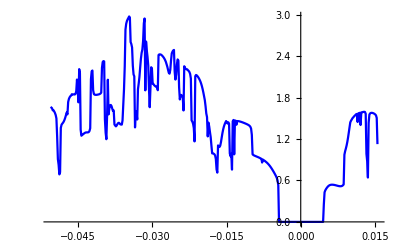

```mathematica
ListLinePlot[z1,PlotStyle->Blue]
```

```mathematica
Dimensions[z]
```

{201,2}

```mathematica
Clear[z1]
```

```mathematica
z[[1]]
```

{-0.488,3.39388}

```mathematica
Dimensions[Table[{ω,tr[ω,0.0001,0.267,0,7]},{ω,Range[-0.49,0.2,0.01]}]]
```

```mathematica
Show[ListLinePlot[Table[{ω,2tr[ω,0.0001,0.267,0,7]},{ω,Range[-0.49,0.2,0.01]}],PlotStyle->Red],ListLinePlot[z]]
```

$Aborted

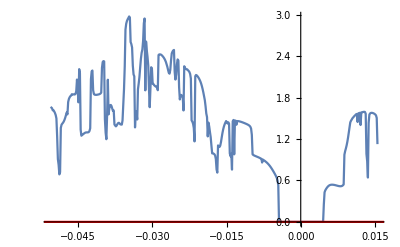

```mathematica
Show[ListLinePlot[z1,PlotRange->All],ListLinePlot[Table[{ω,tr1[ω,0.0001,0.267,0,0.40,7,1]},{ω,Range[-0.8,0.8,0.01]}],PlotStyle->Red]]
```

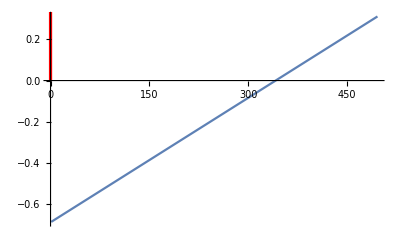

```mathematica
Monitor[Show[ListLinePlot[z],ListLinePlot[Table[{ω,tr1[ω,0.0001,0.267,0,0.40,7,1]},{ω,Range[-0.8,0.8,0.01]}],PlotStyle->Red]],ω]
```

```mathematica
imp1[ω_,δ_,t_,ϵ_,ϵ1_,m_,μ_]:= Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ,μ}}->ω+ⅈ*δ-ϵ1]]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_,m_,μ_]:=Module[{gg=g[ω,δ,t,ϵ,m],x=T1[t,m],T=ρ[t,m]},
η=Module[{c=imp1[ω,δ,t,ϵ,ϵ1,m,μ],c1=imp1[ω,δ,t,ϵ,0,m,μ]},
sl1= Inverse[IdentityMatrix[2m]-c1.ConjugateTranspose[x].SR[ω,δ,t,ϵ,m].x].c1;
sl2= Inverse[IdentityMatrix[2m]-c.ConjugateTranspose[x].SR[ω,δ,t,ϵ,m].x].c;
sl3= Inverse[IdentityMatrix[2m]-c1.ConjugateTranspose[x].SR[ω,δ,t,ϵ,m].x].c1;
Il1:=Inverse[IdentityMatrix[2m]-sl3.T.SR[ω,δ,t,0,m].T].sl3;
Ir1:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,0,m].T.sl3.T].SR[ω,δ,t,0,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,t,0,m].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,δ,t,ϵ,m],tr[ω,δ,t,ϵ,m],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];η]
```

```mathematica
tr1[1,0.0001,0.267,0,.4,7,1]
```

3.87461×10^-8

```mathematica
Clear[tr1]
```

```mathematica
z2
```

```mathematica
Table[tr1[ω,0.0001,0.267,0,0.4,7,1],{ω,{0.,0.2,0.5}}]
```

{3.92767×10^-6,2.,2.}

```mathematica
pris=Table[{ω,Interpolation[Table[{ω,Abs[2tr[ω,0.0001,0.267,0,7]]},{ω,Range[-2,2,0.01]}]][ω]},{ω,Range[-02,2,0.002]}]
```

$Aborted

```mathematica
Clear[pris]
```

```mathematica
Dimensions[%135]
```

{201,2}

```mathematica
f[μ_,ϵ1_]:=NIntegrate[Interpolation[Transpose[Join[{Range[0,2,0.01]},{Abs[Table[{n,Interpolation[Table[{ω,Abs[2tr1[ω,0.0001,0.267,0,ϵ1,7,μ]]},{ω,Range[-0.2,0.2,0.01]}]][n]},{n,Range[-0.2,0.2,0.002]}][[;;,2]]-z[[;;,2]]]}]]][x],{x,0,1}]
```

```mathematica
q[μ_]:=Table[{μ,ϵ1,f[μ,ϵ1]},{ϵ1,-2,2,0.01}]
```

```mathematica
pp=Join[q[1],q[2],q[3],q[4]]
```

Part::partd: Part specification {-0.688,-0.68598,-0.68396,-0.681939,-0.679919,-0.677899,-0.675879,-0.673859,-0.671838,-0.669818,«486»}⟦1;;All,2⟧ is longer than depth of object.

NIntegrate::inumr: The integrand InterpolatingFunction[{{0.,2.}},{5,3,0,{201},{4},0,0,0,0,Automatic,«3»},{{0.,0.01,0.02,«6»,0.09,«191»}},{{Abs[4.00001-1. {«496»}⟦Span[«2»],2⟧]},{Abs[4.00001-1. {«496»}⟦Span[«2»],2⟧]},{Abs[4.-1. {«496»}⟦Span[«2»],2⟧]},«6»,{Abs[4.-1. {«496»}⟦Span[«2»],2⟧]},«191»},{Automatic}][x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.01}}.

Part::partd: Part specification {-0.688,-0.68598,-0.68396,-0.681939,-0.679919,-0.677899,-0.675879,-0.673859,-0.671838,-0.669818,«486»}⟦1;;All,2⟧ is longer than depth of object.

NIntegrate::inumr: The integrand InterpolatingFunction[{{0.,2.}},{5,3,0,{201},{4},0,0,0,0,Automatic,«3»},{{0.,0.01,0.02,«6»,0.09,«191»}},{{Abs[4.00001-1. {«496»}⟦Span[«2»],2⟧]},{Abs[4.00001-1. {«496»}⟦Span[«2»],2⟧]},{Abs[4.-1. {«496»}⟦Span[«2»],2⟧]},«6»,{Abs[4.-1. {«496»}⟦Span[«2»],2⟧]},«191»},{Automatic}][x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.01}}.

Part::partd: Part specification {-0.688,-0.68598,-0.68396,-0.681939,-0.679919,-0.677899,-0.675879,-0.673859,-0.671838,-0.669818,«486»}⟦1;;All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NIntegrate::inumr: The integrand InterpolatingFunction[{{0.,2.}},{5,3,0,{201},{4},0,0,0,0,Automatic,«3»},{{0.,0.01,0.02,«6»,0.09,«191»}},{{Abs[4.00001-1. {«496»}⟦Span[«2»],2⟧]},{Abs[4.00001-1. {«496»}⟦Span[«2»],2⟧]},{Abs[4.-1. {«496»}⟦Span[«2»],2⟧]},«6»,{Abs[4.-1. {«496»}⟦Span[«2»],2⟧]},«191»},{Automatic}][x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.01}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
Position[pp,Min[pp[[;;,3]]]]
pp[[1448]]
```

```mathematica
Interpolation[%52]
```

InterpolatingFunction[…]

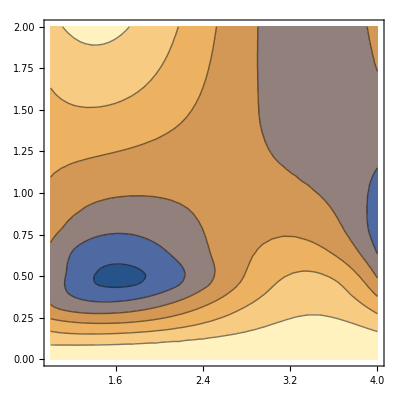

```mathematica
ContourPlot[%59[x,y],{x,1.,4.},{y,0,2.}]
```

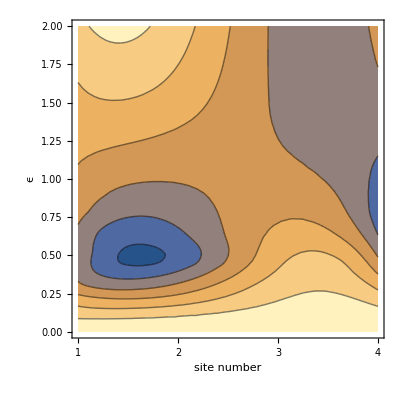

```mathematica
Show[ContourPlot[%59[x,y],{x,1.,4.},{y,0,2.}],FrameLabel->{{HoldForm[ϵ],None},{HoldForm[site number],None}},PlotLabel->None,FrameTicks->{{Automatic,None},{{1,2,3,4},None}},LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}]
```

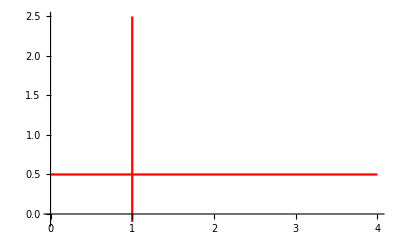

```mathematica
ListLinePlot[{Table[{1,y},{y,Range[0-.1,2.5,0.005]}],Table[{y,0.5},{y,Range[0,4,0.0005]}]},PlotStyle->{{Dashing[{0.01,0.02,2*^-2,1*^-2}],Red},{Dashing[{0.01,0.02,2*^-2,1*^-2}],Red}}]
```

```mathematica
Show[%103]
```

-Graphics-

```mathematica
Min[%237[[;;,3]]]
```

0.228371

```mathematica
%52[[652,2]]
```

0.5

```mathematica
z
```

{{-0.203152,2.87953},{-0.201131,2.84861},{-0.199111,2.88433},{-0.197091,2.84346},{-0.195071,1.98314},{-0.193051,1.89955},{-0.19103,1.97025},{-0.18901,1.51439},{-0.18699,2.9115},{-0.18497,2.95259},{-0.182949,1.95673},{-0.180929,2.9362},{-0.178909,2.93067},{-0.176889,2.81336},{-0.174869,2.9189},{-0.172848,2.91962},{-0.170828,2.91653},{-0.168808,2.91189},{-0.166788,2.90623},{-0.164768,2.89982},{-0.162747,2.89279},{-0.160727,2.88522},{-0.158707,2.8773},{-0.156687,2.86901},{-0.154667,2.86042},{-0.152646,2.85153},{-0.150626,2.84232},{-0.148606,2.83268},{-0.146586,2.8224},{-0.144566,2.81102},{-0.142545,2.79763},{-0.140525,2.7802},{-0.138505,2.75369},{-0.136485,2.70178},{-0.134465,2.51905},{-0.132444,1.95631},{-0.130424,1.93828},{-0.128404,1.92533},{-0.126384,1.91536},{-0.124364,1.90625},{-0.122343,1.89723},{-0.120323,1.8882},{-0.118303,1.87935},{-0.116283,1.86974},{-0.114263,1.86019},{-0.112242,1.84966},{-0.110222,1.83747},{-0.108202,1.8266},{-0.106182,1.71837},{-0.104162,1.80533},{-0.102141,1.78983},{-0.100121,1.77576},{-0.098101,1.76085},{-0.0960808,1.74262},{-0.0940606,1.72533},{-0.0920404,1.7056},{-0.0900202,1.68367},{-0.088,1.66016},{-0.0859798,1.63462},{-0.0839596,1.60693},{-0.0819394,1.5766},{-0.0799192,1.54481},{-0.077899,1.51104},{-0.0758788,1.47576},{-0.0738586,1.43915},{-0.0718384,1.40147},{-0.0698182,1.36208},{-0.067798,1.32011},{-0.0657778,1.27166},{-0.0637576,1.20435},{-0.0617374,1.06333},{-0.0597172,0.},{-0.057697,5.50135×10^-16},{-0.0556768,1.11559×10^-17},{-0.0536566,2.01279×10^-17},{-0.0516364,0.},{-0.0496162,1.11424×10^-18},{-0.047596,2.52037×10^-19},{-0.0455758,3.31854×10^-19},{-0.0435556,0.},{-0.0415354,2.07662×10^-20},{-0.0395152,2.81933×10^-21},{-0.037495,2.03335×10^-21},{-0.0354748,3.06106×10^-21},{-0.0334546,3.57308×10^-21},{-0.0314343,2.7205×10^-22},{-0.0294141,1.12×10^-22},{-0.0273939,2.08963×10^-22},{-0.0253737,1.52841×10^-22},{-0.0233535,6.28547×10^-23},{-0.0213333,0.},{-0.0193131,0.},{-0.0172929,9.16792×10^-23},{-0.0152727,6.72771×10^-23},{-0.0132525,1.91376×10^-22},{-0.0112323,0.},{-0.00921212,0.},{-0.00719192,1.82145×10^-23},{-0.00517172,2.77955×10^-22},{-0.00315152,1.56505×10^-22},{-0.00113131,1.72712×10^-22},{0.00088889,0.},{0.00290909,2.01251×10^-23},{0.00492929,3.7013×10^-23},{0.00694949,2.63239×10^-22},{0.0089697,2.31509×10^-23},{0.0109899,2.14024×10^-22},{0.0130101,5.25148×10^-23},{0.0150303,3.07048×10^-22},{0.0170505,0.},{0.0190707,6.25617×10^-21},{0.0210909,1.08697×10^-22},{0.0231111,1.36106×10^-13},{0.0251313,4.61993×10^-21},{0.0271515,1.74821×10^-21},{0.0291717,4.6572×10^-22},{0.0311919,0.},{0.0332121,1.74996×10^-20},{0.0352323,3.14235×10^-21},{0.0372525,3.06124×10^-14},{0.0392727,1.25623×10^-15},{0.0412929,9.00349×10^-21},{0.0433131,0.},{0.0453333,7.44341×10^-21},{0.0473535,8.86982×10^-22},{0.0493737,0.},{0.0513939,5.31325×10^-18},{0.0534141,5.83418×10^-18},{0.0554343,3.7516×10^-17},{0.0574545,5.41058×10^-17},{0.0594748,2.18383×10^-15},{0.0614949,3.64532×10^-15},{0.0635151,0.506881},{0.0655353,0.856645},{0.0675556,0.913945},{0.0695758,0.951677},{0.071596,0.983738},{0.0736162,1.01141},{0.0756364,1.03415},{0.0776566,1.05151},{0.0796768,1.06387},{0.081697,1.0717},{0.0837172,1.07611},{0.0857374,1.07758},{0.0877576,1.07701},{0.0897778,1.07476},{0.091798,1.07128},{0.0938182,1.06689},{0.0958384,1.06159},{0.0978586,1.05592},{0.0998788,1.05014},{0.101899,1.04442},{0.103919,1.03926},{0.105939,1.03504},{0.10796,1.03256},{0.10998,1.03257},{0.112,1.03607},{0.11402,1.04451},{0.11604,1.05962},{0.118061,1.08494},{0.120081,1.94579},{0.122101,2.04746},{0.124121,2.12606},{0.126141,2.21315},{0.128162,2.31915},{0.130182,2.44626},{0.132202,2.59111},{0.134222,2.73986},{0.136242,2.88322},{0.138263,2.9305},{0.140283,2.9656},{0.142303,3.00273},{0.144323,3.02636},{0.146343,3.05194},{0.148364,3.07514},{0.150384,3.09424},{0.152404,3.11798},{0.154424,3.12552},{0.156444,2.89287},{0.158465,3.14414},{0.160485,3.15129},{0.162505,3.15883},{0.164525,2.80633},{0.166545,3.17048},{0.168566,3.17526},{0.170586,3.18117},{0.172606,3.18556},{0.174626,3.18798},{0.176646,3.18213},{0.178667,3.13106},{0.180687,1.97166},{0.182707,1.75878},{0.184727,1.28489},{0.186747,2.86703},{0.188768,3.10654},{0.190788,3.14236},{0.192808,3.15506},{0.194828,3.15877},{0.196848,3.15651},{0.198869,3.14993},{0.200889,3.14078}}

```mathematica
Dimensions[z]
```

{201,2}

```mathematica
z[[;;,2]]-%326
```

{0.879528,0.84861,0.884324,0.843462,-0.0168585,-0.100451,-0.0297519,-0.485608,0.9115,0.952589,-0.0432664,0.936203,0.93067,0.813364,0.918897,0.919621,0.916532,0.911895,0.906227,0.899818,0.892791,0.885219,0.8773,0.869012,0.860419,0.85153,0.842318,0.832678,0.8224,0.811024,0.797632,0.780204,0.753694,0.701779,0.519054,-0.0436877,-0.0934902,-0.130262,-0.148172,-0.141393,-0.102739,0.07073,0.268268,0.473096,0.670212,0.842734,0.87948,0.885931,0.771255,0.835813,0.789808,0.776069,0.761274,0.742992,0.725539,0.705593,0.683662,0.660162,0.634618,0.606925,0.576601,0.512833,0.455081,0.411815,0.391199,0.40151,0.546029,0.711965,0.879424,1.02003,1.06295,0.0476639,0.0637317,0.0558125,0.0318975,-0.0000223406,-2.80731×10^-6,5.56476×10^-6,5.46949×10^-6,-3.99177×10^-7,-9.3473×10^-6,-8.1487×10^-6,-7.27475×10^-6,-6.66458×10^-6,-6.25732×10^-6,-5.99208×10^-6,-5.60534×10^-6,-5.28956×10^-6,-5.03451×10^-6,-4.82999×10^-6,-4.6658×10^-6,-4.5019×10^-6,-4.36537×10^-6,-4.25344×10^-6,-4.16337×10^-6,-4.0924×10^-6,-4.02929×10^-6,-3.9819×10^-6,-3.94959×10^-6,-3.93172×10^-6,-3.92767×10^-6,-3.93172×10^-6,-3.94959×10^-6,-3.9819×10^-6,-4.02929×10^-6,-4.0924×10^-6,-4.16337×10^-6,-4.25344×10^-6,-4.36537×10^-6,-4.5019×10^-6,-4.6658×10^-6,-4.82999×10^-6,-5.03451×10^-6,-5.28956×10^-6,-5.60534×10^-6,-5.99208×10^-6,-6.25732×10^-6,-6.66458×10^-6,-7.27475×10^-6,-8.1487×10^-6,-9.3473×10^-6,-3.99177×10^-7,5.46949×10^-6,5.56476×10^-6,-2.80731×10^-6,-0.0000223406,0.0318975,0.0558125,0.0637317,0.0476639,-0.000381714,-0.184321,0.114642,0.248499,0.0978947,-0.0482862,-0.0642115,-0.0525419,-0.0218146,0.0195372,0.0638739,0.0717016,0.0761109,0.0775789,0.0770021,0.0747549,0.0714886,0.0672651,0.0620118,0.0562343,0.0501133,0.0749086,0.0921396,0.0943714,0.0745652,0.0256486,-0.153904,-0.352128,-0.551462,-0.732531,-0.0541775,-0.000178968,0.0625208,0.157554,0.28738,0.446268,0.591117,0.739867,0.883222,0.930503,0.965602,1.00273,1.02636,1.05194,1.07514,1.09424,1.11798,1.12552,0.892872,1.14414,1.15129,1.15883,0.806326,1.17048,1.17526,1.18117,1.18556,1.18798,1.18213,1.13106,-0.0283416,-0.241224,-0.715107,0.867034,1.10654,1.14236,1.15506,1.15876,1.1565,1.14992,1.14077}

```mathematica
z[[;;,2]]-%298
```

{2.10957,2.0889,2.13646,2.10835,1.26099,1.18986,1.27184,0.825374,2.22929,2.27391,1.27761,2.24415,2.22228,2.08647,2.1726,2.15427,2.13931,2.12428,2.10956,2.0953,2.08149,2.06676,2.05281,2.03982,2.02804,2.01767,2.01056,2.00469,1.99965,1.99474,1.98881,1.97818,1.95939,1.91626,1.74352,1.19211,1.20896,1.227,1.23875,1.23671,1.21475,1.08737,0.949414,0.814549,0.698236,0.614054,0.688349,0.798224,0.831539,1.06735,1.19454,1.23964,1.26677,1.27594,1.2739,1.25977,1.23947,1.21215,1.17902,1.14169,1.10137,1.0845,1.0628,1.03255,0.989738,0.93045,0.778213,0.617507,0.458147,0.301463,0.10632,-0.851197,-0.710439,-0.548768,-0.38021,-0.218793,-0.145191,-0.0901217,-0.0509523,-0.0250482,-0.00977503,0.00204698,0.0073701,0.00769218,0.00451107,-0.000675369,-0.00103393,-0.00173597,-0.00261745,-0.00351438,-0.00426273,-0.00365811,-0.00283698,-0.00189544,-0.000929563,-0.000035435,0.000174261,0.000249188,0.000222412,0.000126998,-3.98681×10^-6,-7.27804×10^-6,-0.0000125602,-0.000019318,-0.0000270358,-0.0000351984,-0.0000392435,-0.0000437141,-0.0000491066,-0.000055917,-0.0000646418,-0.0000716326,-0.0000825664,-0.0000989755,-0.000122392,-0.000154349,-0.000213779,-0.000280463,-0.000351584,-0.000424325,-0.000495868,-0.000384914,-0.000311747,-0.000318169,-0.000445982,-0.000736989,0.0184006,0.032383,0.03626,0.0250814,-0.00610301,-0.119146,0.259011,0.473646,0.398688,0.316308,0.302511,0.301811,0.309735,0.321911,0.334763,0.329886,0.323152,0.314843,0.305663,0.295792,0.283392,0.271202,0.259528,0.249256,0.240947,0.245082,0.25001,0.253963,0.255575,0.253442,0.233564,0.211255,0.189282,0.172229,0.986455,1.03547,1.05994,1.09317,1.14733,1.22635,1.33862,1.45953,1.579,1.60561,1.62248,1.641,1.64745,1.65702,1.66514,1.66984,1.67777,1.67014,1.42315,1.66112,1.65622,1.65549,1.29578,1.65343,1.65203,1.65171,1.64711,1.64032,1.62524,1.56515,0.397143,0.177714,-0.30225,1.27412,1.50801,1.53823,1.54517,1.54283,1.53406,1.52037,1.50334}

```mathematica
NIntegrate[Interpolation[Transpose[{z[[;;,1]],z[[;;,2]]-%308}]][ω],{ω,-0.2,0.2}]
```

0.264377

```mathematica
z[[;;,2]]-%313
```

{2.10957,2.0889,2.13646,2.10835,1.26099,1.18986,1.27184,0.825374,2.22929,2.27391,1.27761,2.24415,2.22228,2.08647,2.1726,2.15427,2.13931,2.12428,2.10956,2.0953,2.08149,2.06676,2.05281,2.03982,2.02804,2.01767,2.01056,2.00469,1.99965,1.99474,1.98881,1.97818,1.95939,1.91626,1.74352,1.19211,1.20896,1.227,1.23875,1.23671,1.21475,1.08737,0.949414,0.814549,0.698236,0.614054,0.688349,0.798224,0.831539,1.06735,1.19454,1.23964,1.26677,1.27594,1.2739,1.25977,1.23947,1.21215,1.17902,1.14169,1.10137,1.0845,1.0628,1.03255,0.989738,0.93045,0.778213,0.617507,0.458147,0.301463,0.10632,-0.851197,-0.710439,-0.548768,-0.38021,-0.218793,-0.145191,-0.0901217,-0.0509523,-0.0250482,-0.00977503,0.00204698,0.0073701,0.00769218,0.00451107,-0.000675369,-0.00103393,-0.00173597,-0.00261745,-0.00351438,-0.00426273,-0.00365811,-0.00283698,-0.00189544,-0.000929563,-0.000035435,0.000174261,0.000249188,0.000222412,0.000126998,-3.98681×10^-6,-7.27804×10^-6,-0.0000125602,-0.000019318,-0.0000270358,-0.0000351984,-0.0000392435,-0.0000437141,-0.0000491066,-0.000055917,-0.0000646418,-0.0000716326,-0.0000825664,-0.0000989755,-0.000122392,-0.000154349,-0.000213779,-0.000280463,-0.000351584,-0.000424325,-0.000495868,-0.000384914,-0.000311747,-0.000318169,-0.000445982,-0.000736989,0.0184006,0.032383,0.03626,0.0250814,-0.00610301,-0.119146,0.259011,0.473646,0.398688,0.316308,0.302511,0.301811,0.309735,0.321911,0.334763,0.329886,0.323152,0.314843,0.305663,0.295792,0.283392,0.271202,0.259528,0.249256,0.240947,0.245082,0.25001,0.253963,0.255575,0.253442,0.233564,0.211255,0.189282,0.172229,0.986455,1.03547,1.05994,1.09317,1.14733,1.22635,1.33862,1.45953,1.579,1.60561,1.62248,1.641,1.64745,1.65702,1.66514,1.66984,1.67777,1.67014,1.42315,1.66112,1.65622,1.65549,1.29578,1.65343,1.65203,1.65171,1.64711,1.64032,1.62524,1.56515,0.397143,0.177714,-0.30225,1.27412,1.50801,1.53823,1.54517,1.54283,1.53406,1.52037,1.50334}

```mathematica
NIntegrate[Interpolation[Transpose[{z[[;;,1]],%315}]][ω],{ω,-0.2,0.2}]
```

0.323086

```mathematica
NIntegrate[Interpolation[Transpose[{z[[;;,1]],%326}]][ω],{ω,-0.2,0.2}]
```

0.436511

```mathematica
{{0,0.436},{0.1,0.3},{0.2,0.2},{0.3,0.25},{0.4,0.28},{0.5,.29},{0.6,.31},{0.7,0.32},{0.8,.38},{0.9,0.42}}
```

```mathematica
{{0,0.436},{0.1,0.3},{0.2,0.22},{0.3,0.25},{0.4,0.28},{0.5,0.29},{0.6,0.31},{0.7,0.32},{0.8,0.34},{0.9,0.36}}
```

{{0,0.436},{0.1,0.3},{0.2,0.22},{0.3,0.25},{0.4,0.28},{0.5,0.29},{0.6,0.31},{0.7,0.32},{0.8,0.34},{0.9,0.36}}

```mathematica
2933+96+672
```

3701

```mathematica
Interpolation[%44]
```

InterpolatingFunction[…]

```mathematica
{{0,0.436},{0.2,0.28},{0.3,.29},{0.4,.31},{0.5,0.28},{0.6,0.245},{0.7,0.22},{0.8,0.25},{0.9,0.42}}
```

```mathematica
{{0,0.436},{0.2,0.33},{0.3,0.31},{0.4,0.30},{0.5,0.28},{0.6,0.245},{0.7,0.22},{0.8,0.25},{0.9,0.27}}
```

```mathematica
aa={{0,0.3736},{0.2,0.32},{0.3,0.30},{0.4,0.28},{0.5,0.26},{0.6,0.245},{0.7,0.24},{0.8,0.25},{0.9,0.27}}
```

```mathematica
{{0,0.3736},{0.2,0.32},{0.3,0.31},{0.4,0.30},{0.5,0.29},{0.6,0.28},{0.7,0.27},{0.8,0.274},{0.9,0.28}}
```

```mathematica
aa={{0,0.3136},{0.2,0.30},{0.3,0.29},{0.4,0.285},{0.5,0.28},{0.6,0.277},{0.7,0.27},{0.8,0.274},{0.9,0.28}}
```

{{0,0.3136},{0.2,0.3},{0.3,0.29},{0.4,0.285},{0.5,0.28},{0.6,0.277},{0.7,0.27},{0.8,0.274},{0.9,0.28}}

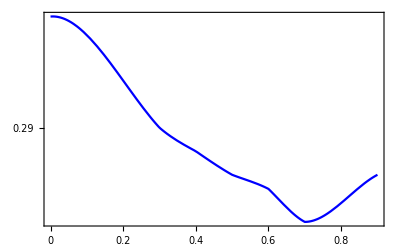

```mathematica
Plot[Interpolation[aa][x],{x,0.,0.9},PlotStyle->Blue,Frame->True,FrameTicks->{{{0.2,0.23,0.26,0.29},None},{{0,0.2,0.4,0.6,.8},None}},PlotRange->All]
```

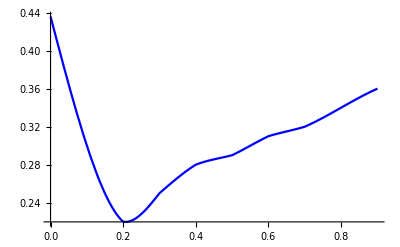

```mathematica
Plot[%45[x],{x,0.,0.9},PlotStyle->Blue]
```

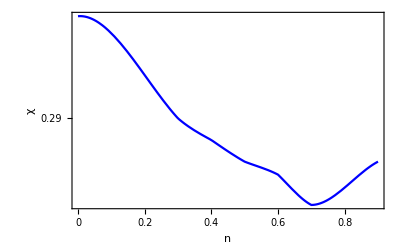

```mathematica
Show[%87,Frame->True,FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

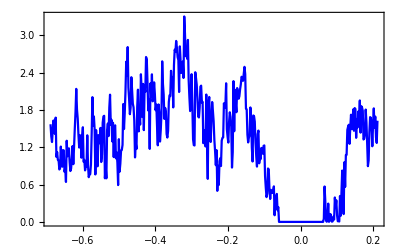

```mathematica
ListLinePlot[Table[{data1[[x]][[1]]+0.372-0.06,data1[[x]][[2]]/2},{x,1,446}],PlotStyle->Blue,Frame->True]
```

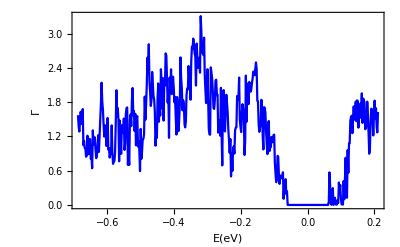

```mathematica
Show[%104,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε[eV]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},FrameTicks->{{Automatic,None},{Automatic,None}}]
```

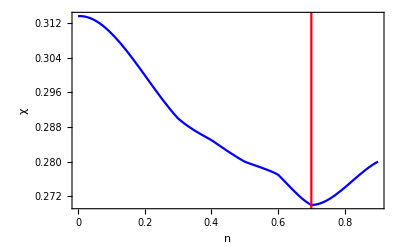

```mathematica
Show[%88,ListLinePlot[{Table[{0.7,y},{y,Range[0,0.5,0.005]}],Table[{0.7,y},{y,Range[0.5,1,0.0005]}]},PlotStyle->{{Dashing[{0.01,0.02,2*^-2,1*^-2}],Red},{Dashing[{1*^-2/2,0.01/2,0.01/2,1*^-2/2}],Black}}(*,PlotRange->{{0,7},{0,7}}*)],LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}]
```

```mathematica
Column[{%112,%114},Spacings->0]
```

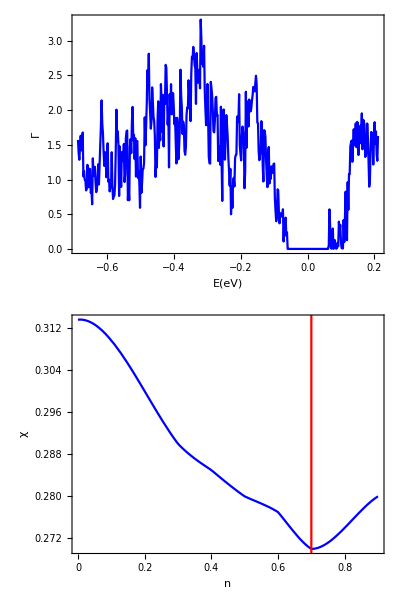

-Graphics-

```mathematica
Export["fig4.eps",%116]
```

fig4.eps

-Graphics-

```mathematica
Export["fig4.eps",%107]
```

fig4.eps

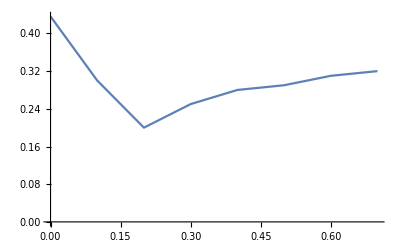

```mathematica
ListPlot[{{0,0.436},{0.1,0.3},{0.2,0.2},{0.3,0.25},{0.4,0.28},{0.5,0.29},{0.6,0.31},{0.7,0.32}},Joined->True]
```

```mathematica
{{0,0.436},{0.2,0.26},{0.7,0.32},{1,0.5}}
```

```mathematica
{{1,0.436},{0.7,0.26},{0.2,0.32},{0,0.5}}
```

{{1,0.436},{0.7,0.26},{0.2,0.32},{0,0.5}}

```mathematica
Interpolation[%133]
```

InterpolatingFunction[…]

```mathematica
Table[InterpolatingFunction[{{0.,1.}},{5,7,0,{4},{4},0,0,0,0,Automatic,{},{},False},{{0.,0.2,0.7,1.}},{Developer`PackedArrayForm,{0,1,2,3,4},{0.35,0.32,0.26,0.32}},{Automatic}][x],{x,Range[0.,0.8,0.01]}]
```

{0.35,0.348887,0.34772,0.346502,0.345234,0.34392,0.34256,0.341158,0.339714,0.338233,0.336714,0.335162,0.333577,0.331963,0.33032,0.328652,0.32696,0.325247,0.323514,0.321765,0.32,0.318223,0.316434,0.314638,0.312834,0.311027,0.309217,0.307408,0.3056,0.303797,0.302,0.300212,0.298434,0.29667,0.29492,0.293188,0.291474,0.289783,0.288114,0.286472,0.284857,0.283273,0.28172,0.280202,0.27872,0.277277,0.275874,0.274515,0.2732,0.271933,0.270714,0.269548,0.268434,0.267377,0.266377,0.265438,0.26456,0.263747,0.263,0.262322,0.261714,0.26118,0.26072,0.260338,0.260034,0.259813,0.259674,0.259622,0.259657,0.259783,0.26,0.260312,0.26072,0.261227,0.261834,0.262545,0.26336,0.264283,0.265314,0.266458,0.267714}

```mathematica
Transpose[Join[{Range[0.,0.8,0.01]},{%148}]]
```

{{0.,0.35},{0.01,0.348887},{0.02,0.34772},{0.03,0.346502},{0.04,0.345234},{0.05,0.34392},{0.06,0.34256},{0.07,0.341158},{0.08,0.339714},{0.09,0.338233},{0.1,0.336714},{0.11,0.335162},{0.12,0.333577},{0.13,0.331963},{0.14,0.33032},{0.15,0.328652},{0.16,0.32696},{0.17,0.325247},{0.18,0.323514},{0.19,0.321765},{0.2,0.32},{0.21,0.318223},{0.22,0.316434},{0.23,0.314638},{0.24,0.312834},{0.25,0.311027},{0.26,0.309217},{0.27,0.307408},{0.28,0.3056},{0.29,0.303797},{0.3,0.302},{0.31,0.300212},{0.32,0.298434},{0.33,0.29667},{0.34,0.29492},{0.35,0.293188},{0.36,0.291474},{0.37,0.289783},{0.38,0.288114},{0.39,0.286472},{0.4,0.284857},{0.41,0.283273},{0.42,0.28172},{0.43,0.280202},{0.44,0.27872},{0.45,0.277277},{0.46,0.275874},{0.47,0.274515},{0.48,0.2732},{0.49,0.271933},{0.5,0.270714},{0.51,0.269548},{0.52,0.268434},{0.53,0.267377},{0.54,0.266377},{0.55,0.265438},{0.56,0.26456},{0.57,0.263747},{0.58,0.263},{0.59,0.262322},{0.6,0.261714},{0.61,0.26118},{0.62,0.26072},{0.63,0.260338},{0.64,0.260034},{0.65,0.259813},{0.66,0.259674},{0.67,0.259622},{0.68,0.259657},{0.69,0.259783},{0.7,0.26},{0.71,0.260312},{0.72,0.26072},{0.73,0.261227},{0.74,0.261834},{0.75,0.262545},{0.76,0.26336},{0.77,0.264283},{0.78,0.265314},{0.79,0.266458},{0.8,0.267714}}

```mathematica
{%149[[1]],%149[[20]],%149[[40]],%149[[60]],%149[[80]],%149[[71]]}
```

{{0.,0.35},{0.19,0.321765},{0.39,0.286472},{0.59,0.262322},{0.79,0.266458},{0.7,0.26}}

```mathematica
Show[ListLinePlot[%149,PlotStyle->Blue],ListPlot[%153,PlotStyle->Directive[Red,PointSize[0.02],"LineOpacity"->1]],Frame->True]
```

-Graphics-

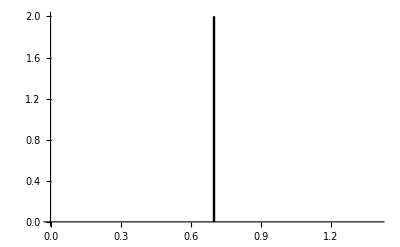

```mathematica
ListLinePlot[{Table[{.7,y},{y,Range[0,2,0.005]}],Table[{.7,y},{y,Range[0.0,2,0.0005]}]},PlotStyle->{{Dashing[{0.01,0.03,1*^-2,1*^-2}],Black},{Dashing[{0.01,0.03,1*^-2,1*^-2}],Black}}]
```

```mathematica
Show[%157,%166,FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},Frame->True,FrameTicks->{{{0.26,0.28,0.30,0.32,0.34},None},{{0,0.2,0.4,0.6,0.8},None}}]
```

-Graphics-

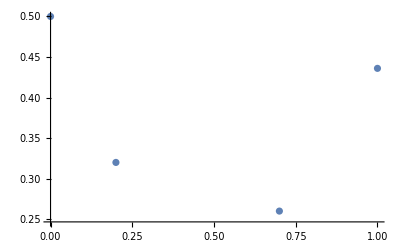

```mathematica
ListPlot[%133]
```

```mathematica
Interpolation[%20]
```

InterpolatingFunction[…]

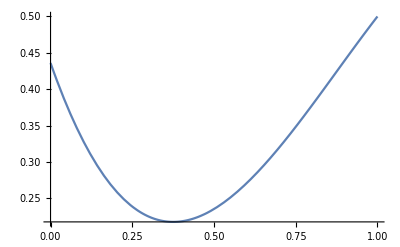

```mathematica
Plot[InterpolatingFunction[{{0.,1.}},{5,7,0,{4},{4},0,0,0,0,Automatic,{},{},False},{{0.,0.2,0.7,1.}},{Developer`PackedArrayForm,{0,1,2,3,4},{0.436,0.26,0.32,0.5}},{Automatic}][x],{x,0.,1.}]
```

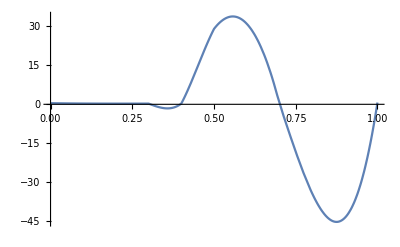

```mathematica
Plot[%8[x],{x,0.,1.}]
```

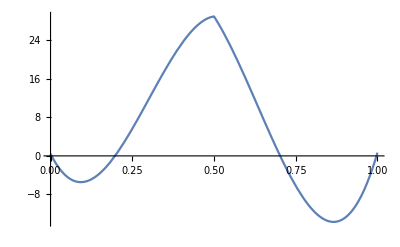

```mathematica
Plot[InterpolatingFunction[{{0.,1.}},{5,7,0,{5},{4},0,0,0,0,Automatic,{},{},False},{{0.,0.2,0.5,0.7,1.}},{Developer`PackedArrayForm,{0,1,2,3,4,5},{0.436,0.264,29.,0.32,0.678}},{Automatic}][x],{x,0.,1.}]
```

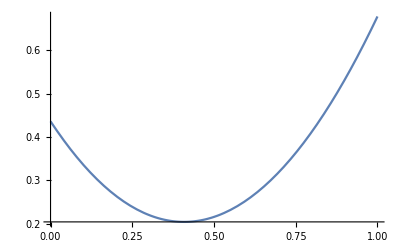

```mathematica
Plot[InterpolatingFunction[{{0.,1.}},{5,7,0,{4},{4},0,0,0,0,Automatic,{},{},False},{{0.,0.2,0.7,1.}},{Developer`PackedArrayForm,{0,1,2,3,4},{0.436,0.264,0.32,0.678}},{Automatic}][x],{x,0.,1.}]
```

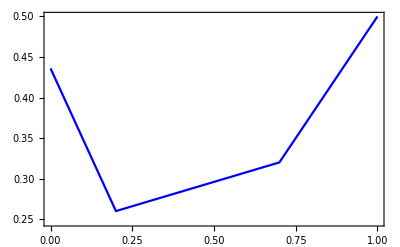

```mathematica
ListLinePlot[%20,Frame->True,PlotStyle->Blue]
```

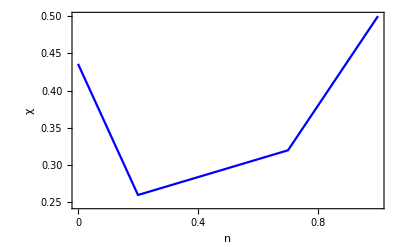

```mathematica
Show[ListLinePlot[%20,Frame->True,PlotStyle->Blue],FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},FrameTicks->{{Automatic,None},{{0,0.2,0.4,0.6,0.8,1},None}}]
```

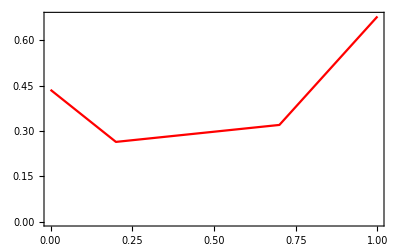

-Graphics-

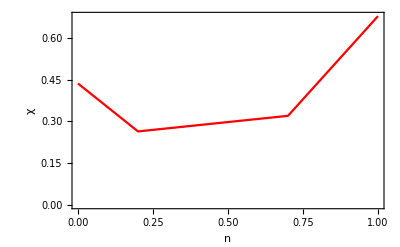

```mathematica
Show[%333,FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

```mathematica
Show[%334,FrameLabel->{{HoldForm[χ],None},{HoldForm[n],HoldForm[DFT transmission=0.2]}},PlotLabel->None]
```

-Graphics-

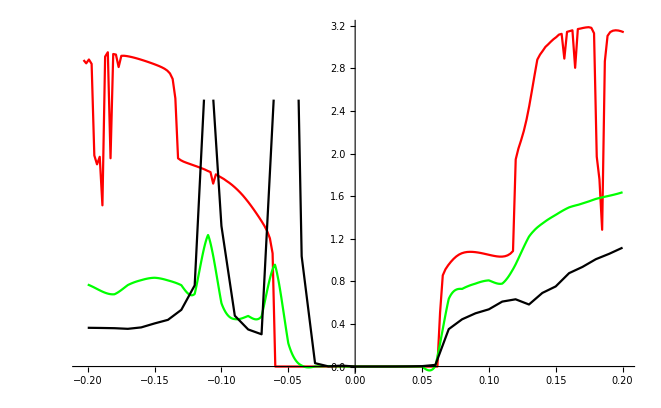

```mathematica
Show[ListLinePlot[z,PlotStyle->Red],%289,%272(*,ListLinePlot[z1,PlotStyle->Blue]*)(*,ListLinePlot[Table[{ω,2tr3[ω,0.0001,0.267,0,+0.5,7,2]},{ω,Range[-0.6,0.2,0.01]}],PlotStyle->Blue]*)]
```

```mathematica
tr3[ω_,δ_,t_,ϵ_,ϵ1_,m_,μ_]:=Module[{gg=g[ω,δ,t,ϵ,m],x=T1[t,m],T=ρ[t,m]},
η=Module[{c=imp1[ω,δ,t,ϵ,ϵ1,m,μ]},
sl1= Inverse[IdentityMatrix[2m]-c.ConjugateTranspose[x].SR[ω,δ,t,ϵ,m].x].c;
Il1:=Inverse[IdentityMatrix[2m]-sl1.T.SR[ω,δ,t,0,m].T].sl1;
Ir1:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,0,m].T.sl1.T].SR[ω,δ,t,0,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,t,0,m].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
η]
```

```mathematica
Clear[imp,imp1,imp2,imp3,imp4]
```

```mathematica
ca[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Module[{gg=g[ω,δ,t,ϵ,m],Tin=T1[t,m],T=ρ[t,m],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}]},
imp2=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]];
imp3=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]];
imp4=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]];
imp=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ1,μ1}}->ω+ⅈ*δ-0]];
tra:=Module[{},lista={RandomSample[{imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp3,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp2,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp}]};
b=Module[{},
sl1= Module[{J=SR[ω,δ,t,0,m]},Do[J=Inverse[IdentityMatrix[2m]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[2m]-sl1.T.SR[ω,δ,t,0,m].T].sl1;
Ir1:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,0,m].T.sl1.T].SR[ω,δ,t,0,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,t,0,m].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,δ,t,ϵ,m],tr[ω,δ,t,ϵ,m],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];b];tra]
```

```mathematica
Timing[Mean[Table[ca[-0.3,0.0001,0.2670,0,0.5,7],1000]]]
```

{12.9559,2.23657}

```mathematica
Table[{ω,Mean[Table[ca[ω,0.0001,0.267,0,0.42,7],1000]]},{ω,Range[-0.8,0.8,0.01]}]
```

{{-0.8,1.49738×10^-6},{-0.79,2.67829×10^-6},{-0.78,6.15439×10^-6},{-0.77,0.0000258232},{-0.76,0.722442},{-0.75,0.63773},{-0.74,0.707051},{-0.73,0.744978},{-0.72,0.789215},{-0.71,0.811658},{-0.7,0.851067},{-0.69,0.861867},{-0.68,0.878687},{-0.67,0.892918},{-0.66,0.908596},{-0.65,0.930284},{-0.64,1.28518},{-0.63,1.32331},{-0.62,1.38112},{-0.61,1.45267},{-0.6,1.49321},{-0.59,1.53652},{-0.58,1.57096},{-0.57,1.60712},{-0.56,1.62925},{-0.55,1.65677},{-0.54,1.67549},{-0.53,1.69186},{-0.52,1.70508},{-0.51,1.73679},{-0.5,1.75875},{-0.49,1.79138},{-0.48,1.83198},{-0.47,1.84239},{-0.46,1.816},{-0.45,1.91069},{-0.44,1.97761},{-0.43,2.02947},{-0.42,2.06813},{-0.41,2.10959},{-0.4,2.1375},{-0.39,2.15787},{-0.38,2.19319},{-0.37,2.22174},{-0.36,2.2178},{-0.35,2.27328},{-0.34,2.2633},{-0.33,2.29563},{-0.32,2.29973},{-0.31,2.34699},{-0.3,2.34143},{-0.29,2.34025},{-0.28,2.36232},{-0.27,2.37674},{-0.26,2.2919},{-0.25,2.05744},{-0.24,1.5297},{-0.23,0.97994},{-0.22,0.890432},{-0.21,0.837658},{-0.2,0.763863},{-0.19,0.757484},{-0.18,0.890811},{-0.17,0.982629},{-0.16,1.04361},{-0.15,1.04196},{-0.14,1.01607},{-0.13,0.938773},{-0.12,0.769124},{-0.11,0.634991},{-0.1,0.432193},{-0.09,0.549705},{-0.08,0.553504},{-0.07,0.509074},{-0.06,0.000364016},{-0.05,0.0000219466},{-0.04,9.21937×10^-6},{-0.03,5.8566×10^-6},{-0.02,4.61937×10^-6},{-0.01,4.00942×10^-6},{0.,3.92628×10^-6},{0.01,4.05764×10^-6},{0.02,4.60969×10^-6},{0.03,5.87564×10^-6},{0.04,9.14247×10^-6},{0.05,0.0000218355},{0.06,0.000352349},{0.07,0.675149},{0.08,0.778192},{0.09,0.818736},{0.1,0.836105},{0.11,0.786933},{0.12,1.08603},{0.13,1.33112},{0.14,1.43586},{0.15,1.5102},{0.16,1.5526},{0.17,1.61337},{0.18,1.63531},{0.19,1.67524},{0.2,1.69298},{0.21,1.7362},{0.22,1.78553},{0.23,1.57413},{0.24,2.01199},{0.25,2.19973},{0.26,2.32677},{0.27,2.38985},{0.28,2.33572},{0.29,2.16427},{0.3,1.84326},{0.31,1.55492},{0.32,1.43963},{0.33,1.45767},{0.34,1.49395},{0.35,1.54247},{0.36,1.61734},{0.37,1.64853},{0.38,1.68686},{0.39,1.71531},{0.4,1.71303},{0.41,1.71073},{0.42,1.69329},{0.43,1.68136},{0.44,1.66347},{0.45,1.65301},{0.46,1.58318},{0.47,1.67274},{0.48,1.05449},{0.49,1.01381},{0.5,0.954454},{0.51,0.869033},{0.52,0.80826},{0.53,0.819188},{0.54,0.844491},{0.55,0.877383},{0.56,0.91994},{0.57,0.943637},{0.58,0.958435},{0.59,0.965856},{0.6,0.97134},{0.61,0.964668},{0.62,0.973019},{0.63,0.956122},{0.64,1.02709},{0.65,0.589931},{0.66,0.379804},{0.67,0.331823},{0.68,0.230368},{0.69,0.214665},{0.7,0.235225},{0.71,0.264218},{0.72,0.286602},{0.73,0.313156},{0.74,0.324973},{0.75,0.36144},{0.76,0.645224},{0.77,0.0000258285},{0.78,6.13308×10^-6},{0.79,2.6788×10^-6},{0.8,1.49298×10^-6}}

```mathematica
Export["3impdft.dat",%33]
```

3impdft.dat

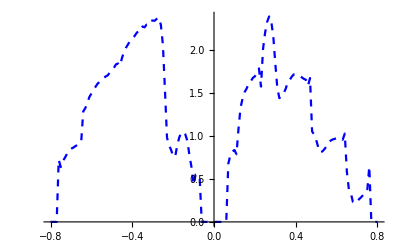

```mathematica
ListPlot[%33,Joined->True,PlotStyle->{Dashed,Blue}]
```

```mathematica
Table[{data1[[x]][[1]]+0.372-0.06,data1[[x]][[2]]/2},{x,241,441}]
```

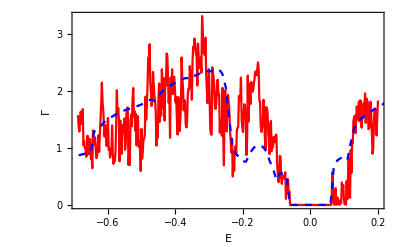

```mathematica
Show[(*ListLinePlot[Table[{data[[x]][[1]]+0.372-0.06,data[[x]][[2]]/2},{x,1,441}],PlotStyle->Red]*)ListLinePlot[Table[{data1[[x]][[1]]+0.372-0.06,data1[[x]][[2]]/2},{x,1,441}],PlotStyle->Red],%174,Frame->True,FrameTicks->{{{0,1,2,3},None},{Automatic,None}},FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε],None}},LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}]
```

```mathematica
Table[{ω,Mean[Table[ca[ω,0.0001,0.267,0,0.5,7],1000]]},{ω,Range[-0.8,0.5,0.01]}]
```

$Aborted

```mathematica
Table[Interpolation[%266][x],{x,-0.2,0.2,0.002}]
```

{0.769966,0.759714,0.747863,0.73511,0.722153,0.709688,0.698411,0.689019,0.682209,0.678677,0.679121,0.692049,0.708393,0.726895,0.7463,0.765349,0.777221,0.787617,0.796671,0.80452,0.811298,0.818456,0.824484,0.82919,0.832378,0.833857,0.83176,0.827983,0.822751,0.816287,0.808815,0.802018,0.794297,0.785514,0.775526,0.764195,0.729319,0.698335,0.676618,0.669543,0.682486,0.800828,0.929937,1.05519,1.16195,1.23561,1.14912,1.02837,0.886835,0.737983,0.595291,0.536113,0.494073,0.466675,0.451424,0.445824,0.444194,0.448019,0.455599,0.465235,0.475226,0.460313,0.448245,0.443214,0.44941,0.471024,0.583867,0.702603,0.813516,0.902891,0.957013,0.851197,0.710439,0.548768,0.38021,0.218793,0.145191,0.0901217,0.0509523,0.0250482,0.00977503,-0.00204698,-0.0073701,-0.00769218,-0.00451107,0.000675369,0.00103393,0.00173597,0.00261745,0.00351438,0.00426273,0.00365811,0.00283698,0.00189544,0.000929563,0.000035435,-0.000174261,-0.000249188,-0.000222412,-0.000126998,3.98681×10^-6,7.27804×10^-6,0.0000125602,0.000019318,0.0000270358,0.0000351984,0.0000392435,0.0000437141,0.0000491066,0.000055917,0.0000646418,0.0000716326,0.0000825664,0.0000989755,0.000122392,0.000154349,0.000213779,0.000280463,0.000351584,0.000424325,0.000495868,0.000384914,0.000311747,0.000318169,0.000445982,0.000736989,-0.0184006,-0.032383,-0.03626,-0.0250814,0.00610301,0.119146,0.24787,0.382998,0.515257,0.63537,0.681227,0.709596,0.724411,0.729604,0.729109,0.741816,0.752961,0.762739,0.771343,0.778968,0.787884,0.795689,0.802058,0.806666,0.809189,0.799342,0.789249,0.781074,0.77698,0.779133,0.80251,0.833258,0.870339,0.912712,0.95934,1.01199,1.06612,1.11998,1.17182,1.21992,1.25249,1.28034,1.30421,1.32489,1.34312,1.36173,1.37891,1.39492,1.41,1.42441,1.44021,1.45538,1.46972,1.48302,1.49507,1.50335,1.51055,1.51705,1.52323,1.52946,1.53845,1.54766,1.55688,1.5659,1.57452,1.58106,1.58714,1.59291,1.59853,1.60413,1.60988,1.61594,1.62245,1.62956,1.63743}

```mathematica
Dimensions[%298]
```

{201}

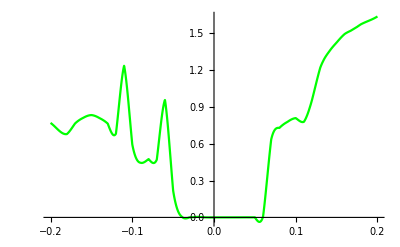

```mathematica
Plot[%273[x],{x,-0.2,0.2},PlotStyle->Green]
```

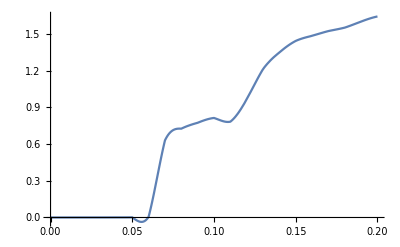

```mathematica
Plot[%262[x],{x,0.,0.2}]
```

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp]
```

```mathematica
ca2[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Module[{gg=g[ω,δ,t,ϵ,m],Tin=T1[t,m],T=ρ[t,m],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
imp2=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]];
imp3=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]];
imp4=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]];
imp5=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]];
imp6=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]];
imp7=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]];
imp8=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]];
imp9=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ9,μ9}}->ω+ⅈ*δ-ϵ1]];
imp10=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ10,μ10}}->ω+ⅈ*δ-ϵ1]];
imp11=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ11,μ11}}->ω+ⅈ*δ-ϵ1]];
imp12=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ12,μ12}}->ω+ⅈ*δ-ϵ1]];
imp5=Inverse[ReplacePart[β[ω,δ,t,ϵ,m],{{μ13,μ13}}->ω+ⅈ*δ-ϵ1]];
imp=Inverse[β[ω,δ,t,ϵ,m]];
tra:=Module[{},lista={RandomSample[{imp,imp,imp,imp,imp,imp5,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp7,imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp,imp10,imp,imp,imp,imp,imp,imp,imp,imp,imp3,imp,imp,imp,imp,imp,imp,imp,imp11,imp,imp,imp,imp,imp,imp,imp2,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp8,imp,imp,imp,imp,imp,imp,imp,imp,imp9,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp6,imp,imp,imp,imp,imp,imp,imp,imp}]};
b=Module[{},
sl1= Module[{J=SR[ω,δ,t,0,m]},Do[J=Inverse[IdentityMatrix[2m]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[2m]-sl1.T.SR[ω,δ,t,0,m].T].sl1;
Ir1:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,0,m].T.sl1.T].SR[ω,δ,t,0,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,t,0,m].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],tr[ω,δ,t,ϵ,ϵ1,m],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];b];tra]
```

```mathematica
Table[{ω,Mean[Table[ca2[ω,0.0001,0.267,0,0.5,7],1000]]},{ω,Range[-2,2,0.01]}]
```

{{-2.,1.05128×10^-9},{-1.99,9.92127×10^-10},{-1.98,1.07328×10^-9},{-1.97,1.00548×10^-9},{-1.96,1.24745×10^-9},{-1.95,1.08724×10^-9},{-1.94,1.12648×10^-9},{-1.93,1.16595×10^-9},{-1.92,1.23827×10^-9},{-1.91,1.22877×10^-9},{-1.9,1.34811×10^-9},{-1.89,1.66301×10^-9},{-1.88,1.68687×10^-9},{-1.87,1.36403×10^-9},{-1.86,1.44037×10^-9},{-1.85,1.83117×10^-9},{-1.84,1.62713×10^-9},{-1.83,1.72233×10^-9},{-1.82,1.63639×10^-9},{-1.81,2.09397×10^-9},{-1.8,2.1083×10^-9},{-1.79,2.12811×10^-9},{-1.78,2.02184×10^-9},{-1.77,2.27606×10^-9},{-1.76,2.50882×10^-9},{-1.75,2.43195×10^-9},{-1.74,3.09488×10^-9},{-1.73,3.19308×10^-9},{-1.72,2.55605×10^-9},{-1.71,2.67129×10^-9},{-1.7,3.62921×10^-9},{-1.69,3.61023×10^-9},{-1.68,2.54712×10^-9},{-1.67,3.75283×10^-9},{-1.66,3.27808×10^-9},{-1.65,3.97041×10^-9},{-1.64,5.0305×10^-9},{-1.63,4.70048×10^-9},{-1.62,3.87163×10^-9},{-1.61,5.70676×10^-9},{-1.6,6.28336×10^-9},{-1.59,5.58122×10^-9},{-1.58,7.92567×10^-9},{-1.57,6.24037×10^-9},{-1.56,4.7844×10^-9},{-1.55,6.8238×10^-9},{-1.54,7.80617×10^-9},{-1.53,9.5266×10^-9},{-1.52,1.23526×10^-8},{-1.51,8.897×10^-9},{-1.5,9.72964×10^-9},{-1.49,1.11941×10^-8},{-1.48,9.56075×10^-9},{-1.47,1.46851×10^-8},{-1.46,1.57175×10^-8},{-1.45,1.12267×10^-8},{-1.44,1.56449×10^-8},{-1.43,2.24619×10^-8},{-1.42,1.70416×10^-8},{-1.41,2.03404×10^-8},{-1.4,1.63268×10^-8},{-1.39,1.51232×10^-8},{-1.38,2.5428×10^-8},{-1.37,2.24262×10^-8},{-1.36,3.04016×10^-8},{-1.35,2.36055×10^-8},{-1.34,2.91845×10^-8},{-1.33,2.55507×10^-8},{-1.32,3.63633×10^-8},{-1.31,3.34707×10^-8},{-1.3,4.949×10^-8},{-1.29,3.10089×10^-8},{-1.28,6.82588×10^-8},{-1.27,6.44592×10^-8},{-1.26,5.5273×10^-8},{-1.25,4.98579×10^-8},{-1.24,6.60044×10^-8},{-1.23,6.72683×10^-8},{-1.22,6.00898×10^-8},{-1.21,1.09129×10^-7},{-1.2,1.2762×10^-7},{-1.19,1.21835×10^-7},{-1.18,9.64298×10^-8},{-1.17,1.21198×10^-7},{-1.16,1.07607×10^-7},{-1.15,2.61601×10^-7},{-1.14,2.0457×10^-7},{-1.13,2.86772×10^-7},{-1.12,2.47121×10^-7},{-1.11,2.96856×10^-7},{-1.1,2.79458×10^-7},{-1.09,2.91997×10^-7},{-1.08,3.83906×10^-7},{-1.07,3.42527×10^-7},{-1.06,4.88474×10^-7},{-1.05,7.49567×10^-7},{-1.04,7.13198×10^-7},{-1.03,6.03974×10^-7},{-1.02,9.85985×10^-7},{-1.01,7.92688×10^-7},{-1.,8.04571×10^-7},{-0.99,1.21178×10^-6},{-0.98,1.5585×10^-6},{-0.97,2.12302×10^-6},{-0.96,1.7851×10^-6},{-0.95,3.01184×10^-6},{-0.94,2.36119×10^-6},{-0.93,4.25241×10^-6},{-0.92,4.0742×10^-6},{-0.91,7.0486×10^-6},{-0.9,9.64655×10^-6},{-0.89,0.0000104384},{-0.88,9.51066×10^-6},{-0.87,0.0000156129},{-0.86,0.0000184886},{-0.85,0.0000230788},{-0.84,0.000027402},{-0.83,0.0000276501},{-0.82,0.0000492602},{-0.81,0.000070395},{-0.8,0.000113425},{-0.79,0.000112052},{-0.78,0.000407954},{-0.77,0.000806451},{-0.76,0.398132},{-0.75,0.361295},{-0.74,0.406741},{-0.73,0.451469},{-0.72,0.502202},{-0.71,0.538261},{-0.7,0.570071},{-0.69,0.603806},{-0.68,0.629134},{-0.67,0.669316},{-0.66,0.715052},{-0.65,0.755411},{-0.64,0.740138},{-0.63,0.72683},{-0.62,0.761615},{-0.61,0.828891},{-0.6,0.874393},{-0.59,0.926205},{-0.58,0.958512},{-0.57,0.99127},{-0.56,1.03752},{-0.55,1.06564},{-0.54,1.11993},{-0.53,1.14496},{-0.52,1.20206},{-0.51,1.22594},{-0.5,1.2952},{-0.49,1.35905},{-0.48,1.45947},{-0.47,1.14502},{-0.46,0.816936},{-0.45,0.894817},{-0.44,0.944131},{-0.43,1.00515},{-0.42,1.03705},{-0.41,1.06604},{-0.4,1.11532},{-0.39,1.14325},{-0.38,1.17275},{-0.37,1.19984},{-0.36,1.20266},{-0.35,1.2265},{-0.34,1.24952},{-0.33,1.27581},{-0.32,1.28483},{-0.31,1.3349},{-0.3,1.32283},{-0.29,1.34947},{-0.28,1.35012},{-0.27,1.3317},{-0.26,1.22349},{-0.25,0.978006},{-0.24,0.63381},{-0.23,1.06485},{-0.22,0.807257},{-0.21,0.431031},{-0.2,0.3644},{-0.19,0.339473},{-0.18,0.366192},{-0.17,0.35296},{-0.16,0.380404},{-0.15,0.386527},{-0.14,0.423876},{-0.13,0.509494},{-0.12,0.772506},{-0.11,3.14683},{-0.1,1.3402},{-0.09,0.469313},{-0.08,0.313442},{-0.07,0.312137},{-0.06,3.21159},{-0.05,7.77373},{-0.04,0.0393111},{-0.03,0.0325215},{-0.02,0.0016521},{-0.01,0.00018495},{0.,0.0000296185},{0.01,0.000466007},{0.02,0.00022726},{0.03,0.000666482},{0.04,0.00140782},{0.05,0.00332436},{0.06,0.0166929},{0.07,0.347161},{0.08,0.438773},{0.09,0.512033},{0.1,0.542717},{0.11,0.602719},{0.12,0.659614},{0.13,0.582978},{0.14,0.690069},{0.15,0.766565},{0.16,0.861106},{0.17,0.9358},{0.18,1.00194},{0.19,1.0759},{0.2,1.10443},{0.21,1.20199},{0.22,1.2815},{0.23,0.877291},{0.24,0.887816},{0.25,1.09744},{0.26,1.23649},{0.27,1.31694},{0.28,1.31859},{0.29,1.14466},{0.3,0.934891},{0.31,0.66711},{0.32,0.565933},{0.33,0.508418},{0.34,0.484485},{0.35,0.535286},{0.36,0.561182},{0.37,0.597417},{0.38,0.594177},{0.39,0.616611},{0.4,0.62595},{0.41,0.662654},{0.42,0.659221},{0.43,0.62585},{0.44,0.62465},{0.45,0.64036},{0.46,0.639805},{0.47,1.13166},{0.48,0.596594},{0.49,0.423626},{0.5,0.413426},{0.51,0.41257},{0.52,0.406852},{0.53,0.350156},{0.54,0.333707},{0.55,0.318965},{0.56,0.325657},{0.57,0.337797},{0.58,0.342158},{0.59,0.34764},{0.6,0.354862},{0.61,0.361138},{0.62,0.38528},{0.63,0.400496},{0.64,0.48484},{0.65,0.325473},{0.66,0.201619},{0.67,0.178505},{0.68,0.202527},{0.69,0.167069},{0.7,0.180354},{0.71,0.153941},{0.72,0.105532},{0.73,0.128354},{0.74,0.139081},{0.75,0.153931},{0.76,0.322099},{0.77,0.0137933},{0.78,0.120606},{0.79,0.145264},{0.8,0.00907596},{0.81,0.00810762},{0.82,0.0144672},{0.83,0.0462206},{0.84,0.571889},{0.85,0.0769499},{0.86,0.350794},{0.87,0.017407},{0.88,0.00309151},{0.89,0.00145121},{0.9,0.000908352},{0.91,0.000568979},{0.92,0.000289849},{0.93,0.000239845},{0.94,0.000221068},{0.95,0.000100865},{0.96,0.0000952965},{0.97,0.0000524986},{0.98,0.0000452689},{0.99,0.0000415401},{1.,0.0000489182},{1.01,0.0000175187},{1.02,0.00001586},{1.03,0.0000170568},{1.04,9.95108×10^-6},{1.05,0.000013076},{1.06,6.1817×10^-6},{1.07,8.44131×10^-6},{1.08,5.23619×10^-6},{1.09,6.05376×10^-6},{1.1,5.50501×10^-6},{1.11,2.7745×10^-6},{1.12,2.76651×10^-6},{1.13,2.52336×10^-6},{1.14,2.08788×10^-6},{1.15,1.8609×10^-6},{1.16,1.38675×10^-6},{1.17,1.15322×10^-6},{1.18,1.37099×10^-6},{1.19,1.08656×10^-6},{1.2,8.8376×10^-7},{1.21,7.50626×10^-7},{1.22,6.11631×10^-7},{1.23,9.36818×10^-7},{1.24,4.55714×10^-7},{1.25,3.20085×10^-7},{1.26,2.84703×10^-7},{1.27,4.57439×10^-7},{1.28,4.05917×10^-7},{1.29,2.91245×10^-7},{1.3,2.06048×10^-7},{1.31,2.00176×10^-7},{1.32,1.86803×10^-7},{1.33,1.22466×10^-7},{1.34,1.51118×10^-7},{1.35,7.8251×10^-8},{1.36,1.22754×10^-7},{1.37,1.4051×10^-7},{1.38,1.38548×10^-7},{1.39,8.05482×10^-8},{1.4,7.6051×10^-8},{1.41,8.06399×10^-8},{1.42,8.36687×10^-8},{1.43,5.04659×10^-8},{1.44,5.24079×10^-8},{1.45,7.50413×10^-8},{1.46,5.265×10^-8},{1.47,7.55673×10^-8},{1.48,4.712×10^-8},{1.49,5.66763×10^-8},{1.5,2.4926×10^-8},{1.51,3.76195×10^-8},{1.52,3.35605×10^-8},{1.53,3.66055×10^-8},{1.54,3.63532×10^-8},{1.55,2.55497×10^-8},{1.56,1.62461×10^-8},{1.57,2.52287×10^-8},{1.58,1.96109×10^-8},{1.59,1.76088×10^-8},{1.6,2.48399×10^-8},{1.61,1.91108×10^-8},{1.62,2.09204×10^-8},{1.63,1.1473×10^-8},{1.64,9.53824×10^-9},{1.65,1.28631×10^-8},{1.66,8.33026×10^-9},{1.67,9.33994×10^-9},{1.68,7.88037×10^-9},{1.69,9.25335×10^-9},{1.7,7.91774×10^-9},{1.71,7.19491×10^-9},{1.72,8.45665×10^-9},{1.73,6.34664×10^-9},{1.74,7.25793×10^-9},{1.75,6.99227×10^-9},{1.76,5.60652×10^-9},{1.77,5.133×10^-9},{1.78,4.70091×10^-9},{1.79,3.52155×10^-9},{1.8,4.43502×10^-9},{1.81,4.98502×10^-9},{1.82,4.27726×10^-9},{1.83,3.44538×10^-9},{1.84,3.63964×10^-9},{1.85,3.80107×10^-9},{1.86,3.51736×10^-9},{1.87,2.86972×10^-9},{1.88,2.94269×10^-9},{1.89,2.45525×10^-9},{1.9,2.71806×10^-9},{1.91,2.23098×10^-9},{1.92,2.29277×10^-9},{1.93,2.34073×10^-9},{1.94,2.08866×10^-9},{1.95,2.26208×10^-9},{1.96,2.29291×10^-9},{1.97,1.68932×10^-9},{1.98,2.04096×10^-9},{1.99,1.47792×10^-9},{2.,1.58945×10^-9}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/DFT/7AGNR/10imp.dat",%360]
```

/home/shardulmukim/PhD/fwi/DFT/7AGNR/10imp.dat

```mathematica
Clear[conavg10,conavg3]
```

```mathematica
conavg10:=conavg10=Table[{m,Interpolation[Import["/home/shardulmukim/PhD/fwi/DFT/7AGNR/10imp.dat"]][m]},{m,Range[-2,2,0.002]}]
```

```mathematica
Dimensions[conavg3]
```

{2001}

```mathematica
conavg3:=conavg3= Table[{m,Interpolation[Import["/home/shardulmukim/PhD/fwi/DFT/7AGNR/3imp.dat"]][m]},{m,Range[-2,2,0.002]}]
```

```mathematica
ListPlot[%360,Joined->True,PlotStyle->Black]
```

```mathematica
Interpolation[%268]
```

InterpolatingFunction[…]

```mathematica
Table[Interpolation[%266][x],{x,-0.2,0.2,0.002}]
```

{0.769966,0.759714,0.747863,0.73511,0.722153,0.709688,0.698411,0.689019,0.682209,0.678677,0.679121,0.692049,0.708393,0.726895,0.7463,0.765349,0.777221,0.787617,0.796671,0.80452,0.811298,0.818456,0.824484,0.82919,0.832378,0.833857,0.83176,0.827983,0.822751,0.816287,0.808815,0.802018,0.794297,0.785514,0.775526,0.764195,0.729319,0.698335,0.676618,0.669543,0.682486,0.800828,0.929937,1.05519,1.16195,1.23561,1.14912,1.02837,0.886835,0.737983,0.595291,0.536113,0.494073,0.466675,0.451424,0.445824,0.444194,0.448019,0.455599,0.465235,0.475226,0.460313,0.448245,0.443214,0.44941,0.471024,0.583867,0.702603,0.813516,0.902891,0.957013,0.851197,0.710439,0.548768,0.38021,0.218793,0.145191,0.0901217,0.0509523,0.0250482,0.00977503,-0.00204698,-0.0073701,-0.00769218,-0.00451107,0.000675369,0.00103393,0.00173597,0.00261745,0.00351438,0.00426273,0.00365811,0.00283698,0.00189544,0.000929563,0.000035435,-0.000174261,-0.000249188,-0.000222412,-0.000126998,3.98681×10^-6,7.27804×10^-6,0.0000125602,0.000019318,0.0000270358,0.0000351984,0.0000392435,0.0000437141,0.0000491066,0.000055917,0.0000646418,0.0000716326,0.0000825664,0.0000989755,0.000122392,0.000154349,0.000213779,0.000280463,0.000351584,0.000424325,0.000495868,0.000384914,0.000311747,0.000318169,0.000445982,0.000736989,-0.0184006,-0.032383,-0.03626,-0.0250814,0.00610301,0.119146,0.24787,0.382998,0.515257,0.63537,0.681227,0.709596,0.724411,0.729604,0.729109,0.741816,0.752961,0.762739,0.771343,0.778968,0.787884,0.795689,0.802058,0.806666,0.809189,0.799342,0.789249,0.781074,0.77698,0.779133,0.80251,0.833258,0.870339,0.912712,0.95934,1.01199,1.06612,1.11998,1.17182,1.21992,1.25249,1.28034,1.30421,1.32489,1.34312,1.36173,1.37891,1.39492,1.41,1.42441,1.44021,1.45538,1.46972,1.48302,1.49507,1.50335,1.51055,1.51705,1.52323,1.52946,1.53845,1.54766,1.55688,1.5659,1.57452,1.58106,1.58714,1.59291,1.59853,1.60413,1.60988,1.61594,1.62245,1.62956,1.63743}

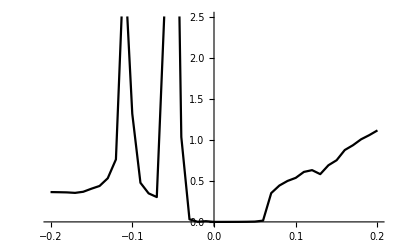

```mathematica
ListPlot[%268,Joined->True,PlotStyle->Black]
```

```mathematica
z:=z=Table[{data[[x]][[1]]+0.372-0.06,data[[x]][[2]]/2},{x,1,496}]
```

```mathematica
z1:=z1=Table[{data1[[x]][[1]]+0.372-0.06,data1[[x]][[2]]/2},{x,1,496}]
```

```mathematica
z[[2]]
```

{-0.68598,3.31265}

```mathematica
conavg3[[657]]
```

{-0.688,0.838743}

```mathematica
conavg3[[657+496]]
```

{0.304,1.78276}

```mathematica
conavg10[[133]]
```

{-0.68,0.629134}

```mathematica
Dimensions[z]
```

{496,2}

```mathematica
Clear[z,z1]
```

```mathematica
Module[{},(*ρ0=Module[{B1=Transpose[Join[{z[[;;,1]]},{Abs[Take[pris[[657;;657+495]]][[;;,2]]-z[[;;,2]]]}]]},Integrate[Interpolation[B1][ω],{ω,-0.0,0.1}]];*)ρ3=Module[{B1=Transpose[Join[{z1[[;;,1]]},{Abs[Take[conavg3[[657;;657+495]]][[;;,2]]-z[[;;,2]]]}]]},Integrate[Interpolation[B1][ω],{ω,-0.0,0.1}]];
ρ10=Module[{B1=Transpose[Join[{z1[[;;,1]]},{Abs[Take[conavg10[[657;;657+495]]][[;;,2]]-z[[;;,2]]]}]]},Integrate[Interpolation[B1][ω],{ω,-0.0,0.1}]];{ρ0,ρ3,ρ10}]
```

{ρ0,0.0182412,0.0258338}

```mathematica
Module[{B1=Transpose[Join[{z[[;;,1]]},{Abs[Take[pris[[657;;657+495]]][[;;,2]]-z[[;;,2]]]}]]},Integrate[Interpolation[B1][ω],{ω,-0.0,0.1}]]
```

$Aborted

```mathematica
pris
```

$Aborted

```mathematica
Module[{B1=Transpose[Join[{z1[[;;,1]]},{Abs[2Take[conavg10[[657;;657+495]]][[;;,2]]-z1[[;;,2]]]}]]},Integrate[Interpolation[B1][ω],{ω,-0.0,0.1}]]
```

0.0220775

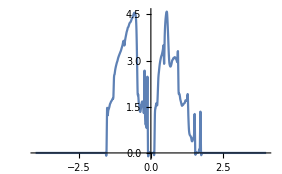

```mathematica
ListLinePlot[2conavg3]
```

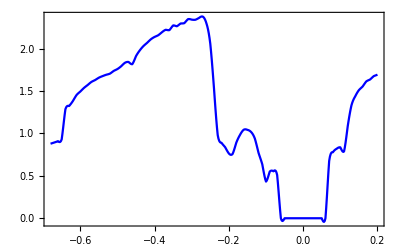

```mathematica
ListPlot[Table[{x,Interpolation[Import["3impdft.dat"][[13;;102]]][x]},{x,Range[-0.68,0.2,0.89/445]}],Joined->True,PlotStyle->Blue,Frame->True]
```

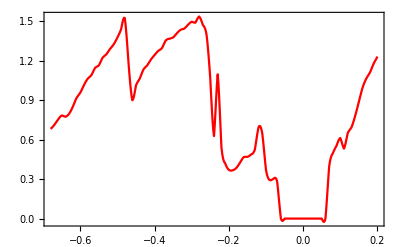

```mathematica
ListLinePlot[Table[{x,Interpolation[Import["10impdft.dat"][[13;;102]]][x]},{x,Range[-0.68,0.2,0.89/445]}],PlotStyle->Red,Frame->True]
```

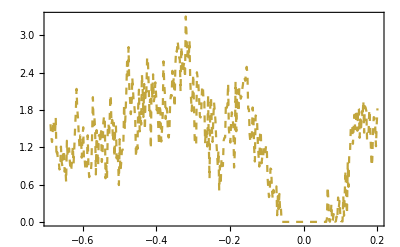

```mathematica
ListLinePlot[Table[{data1[[x]][[1]]+0.372-0.06,data1[[x]][[2]]/2},{x,1,441}],PlotStyle->{Dashed,RGBColor[0.76,0.65,0.24]},Frame->True]
```

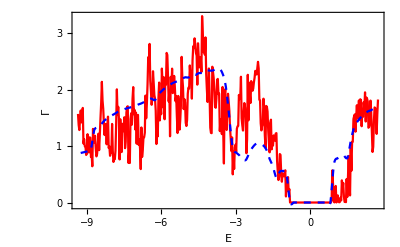

```mathematica
Show[ListLinePlot[Table[{(data1[[x]][[1]]+0.372-0.06)*13.6,data1[[x]][[2]]/2},{x,1,441}],PlotStyle->Red,Frame->True],ListPlot[Table[{x*13.6,Interpolation[Import["3impdft.dat"][[13;;102]]][x]},{x,Range[-0.68,0.2,0.89/445]}],Joined->True,PlotStyle->{Blue,Dashed},Frame->True],PlotRange->All,FrameTicks->{{{0,1,2,3},None},{Automatic,None}},FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε],None}},LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}(*Epilog->{Text[Style["(b)","Times New Roman",18],{0.2,2.8}]},*)]
```

```mathematica
Show[Show[ListLinePlot[z,PlotStyle->Blue],ListLinePlot[Table[{ω,tr1[ω,0.0001,0.267,0,0.40,7,1]},{ω,Range[-0.8,0.8,0.01]}],PlotStyle->{Dashed,Red}]],Frame->True,FrameTicks->{{{0,1,2,3},None},{Automatic,None}},FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε],None}},LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}]
```

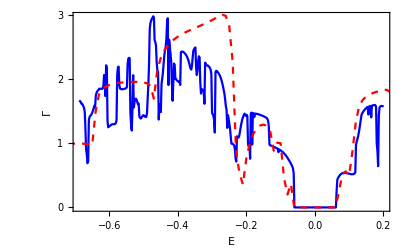

-Graphics-

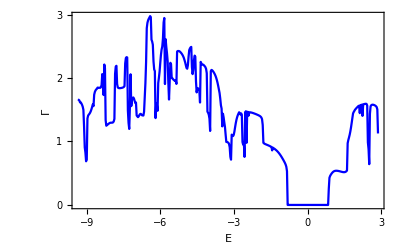

```mathematica
Show[ListLinePlot[z1,PlotStyle->Blue],]
```

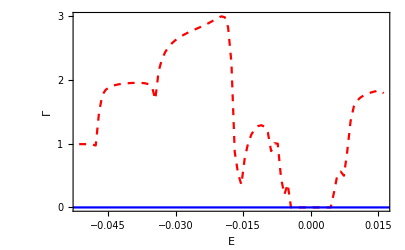

```mathematica
Show[ListLinePlot[Table[{ω/13.6,If[tr3[ω,0.0001,0.267,0,0.40,7,1]>tr[ω,0.0001,0.267,0,7],tr[ω,0.0001,0.267,0,7],tr3[ω,0.0001,0.267,0,0.40,7,1]]},{ω,Range[-0.7,0.22,0.01]}],PlotStyle->{Dashed,Red}],%67,Frame->True,FrameTicks->{{{0,1,2,3},None},{Automatic,None}},FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε],None}},LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]}]
```

```mathematica
tr3[ω_,δ_,t_,ϵ_,ϵ1_,m_,μ_]:=Module[{gg=g[ω,δ,t,ϵ,m],x=T1[t,m],T=ρ[t,m]},
η=Module[{c=imp1[ω,δ,t,ϵ,ϵ1,m,μ]},
sl1= Inverse[IdentityMatrix[2m]-c.ConjugateTranspose[x].SR[ω,δ,t,ϵ,m].x].c;
Il1:=Inverse[IdentityMatrix[2m]-sl1.T.SR[ω,δ,t,0,m].T].sl1;
Ir1:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,0,m].T.sl1.T].SR[ω,δ,t,0,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,t,0,m].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
η]
```

```mathematica
Table[{ω/13.6,If[tr3[ω,0.0001,0.267,0,0.40,7,1]>tr[ω,0.0001,0.267,0,7],tr[ω,0.0001,0.267,0,7],tr3[ω,0.0001,0.267,0,0.40,7,1]]},{ω,Range[-0.7,0.3,0.01]}]
```

{{-0.0514706,0.992821},{-0.0507353,0.992884},{-0.05,0.992383},{-0.0492647,0.990934},{-0.0485294,0.987102},{-0.0477941,0.971489},{-0.0470588,1.48863},{-0.0463235,1.76441},{-0.0455882,1.84458},{-0.0448529,1.88324},{-0.0441176,1.90609},{-0.0433824,1.92119},{-0.0426471,1.93184},{-0.0419118,1.93965},{-0.0411765,1.94547},{-0.0404412,1.94976},{-0.0397059,1.95272},{-0.0389706,1.95438},{-0.0382353,1.9545},{-0.0375,1.95244},{-0.0367647,1.94666},{-0.0360294,1.93279},{-0.0352941,1.89313},{-0.0345588,1.69395},{-0.0338235,2.13493},{-0.0330882,2.32412},{-0.0323529,2.43774},{-0.0316176,2.51592},{-0.0308824,2.57427},{-0.0301471,2.62035},{-0.0294118,2.65837},{-0.0286765,2.69085},{-0.0279412,2.7195},{-0.0272059,2.74549},{-0.0264706,2.76972},{-0.0257353,2.79294},{-0.025,2.8158},{-0.0242647,2.83891},{-0.0235294,2.86291},{-0.0227941,2.8884},{-0.0220588,2.91593},{-0.0213235,2.94556},{-0.0205882,2.9756},{-0.0198529,2.99807},{-0.0191176,2.98267},{-0.0183824,2.82466},{-0.0176471,2.27254},{-0.0169118,0.870611},{-0.0161765,0.532602},{-0.0154412,0.356605},{-0.0147059,0.763332},{-0.0139706,0.998864},{-0.0132353,1.14095},{-0.0125,1.22703},{-0.0117647,1.27472},{-0.0110294,1.28991},{-0.0102941,1.26736},{-0.00955882,1.17842},{-0.00882353,0.883351},{-0.00808824,1.00693},{-0.00735294,1.00002},{-0.00661765,0.457088},{-0.00588235,0.201578},{-0.00514706,0.367145},{-0.00441176,0.000381714},{-0.00367647,0.0000223406},{-0.00294118,9.3473×10^-6},{-0.00220588,5.99208×10^-6},{-0.00147059,4.6658×10^-6},{-0.000735294,4.0924×10^-6},{8.1634×10^-18,3.92767×10^-6},{0.000735294,4.0924×10^-6},{0.00147059,4.6658×10^-6},{0.00220588,5.99208×10^-6},{0.00294118,9.3473×10^-6},{0.00367647,0.0000223406},{0.00441176,0.000381714},{0.00514706,0.237339},{0.00588235,0.507951},{0.00661765,0.562178},{0.00735294,0.497394},{0.00808824,0.882685},{0.00882353,1.35139},{0.00955882,1.5871},{0.0102941,1.67591},{0.0110294,1.72485},{0.0117647,1.7572},{0.0125,1.78108},{0.0132353,1.8},{0.0139706,1.81543},{0.0147059,1.82717},{0.0154412,1.83107},{0.0161765,1.79225},{0.0169118,2.70768},{0.0176471,2.89835},{0.0183824,2.95469},{0.0191176,2.99012},{0.0198529,2.99755},{0.0205882,2.93367},{0.0213235,2.7144},{0.0220588,2.32077}}

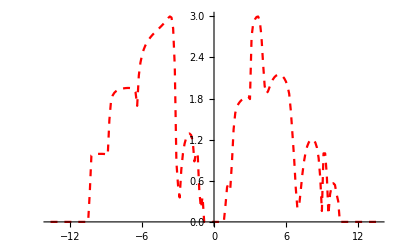

```mathematica
ListPlot[%102,Joined->True,PlotStyle->{Dashed,Red}]
```

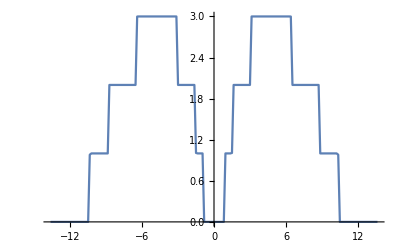

```mathematica
ListPlot[%89,Joined->True]
```